## Set up the metric, compute the Einstein tensor etc.

```mathematica
NotebookDirectory[]
```

/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo

### Metric and reference metric

```mathematica
Clear[Afun,Sfun,Φfun,Vfun]
```

```mathematica
co = {r,t,x1,x2,x3};
Ndim = Length[co];
```

```mathematica
(*g=({{0, 1, 0, 0, 0}, {1, -Afun[r,t], 0, 0, 0}, {0, 0, r^2 Exp[Sfun[r,t]], 0, 0}, {0, 0, 0, r^2 Exp[Sfun[r,t]], 0}, {0, 0, 0, 0, r^2 Exp[Sfun[r,t]]}});*)
g=({{0, 1, 0, 0, 0}, {1, -Afun[r,t], 0, 0, 0}, {0, 0, Sfun[r,t]^2, 0, 0}, {0, 0, 0, Sfun[r,t]^2, 0}, {0, 0, 0, 0, Sfun[r,t]^2}});
gup=Inverse[g]//Simplify;
```

### Christoffel Symbols

```mathematica
Chr=Table[
Simplify[(1/2)*Sum[gup[[μ,α]]*(
D[g[[ν,α]],co[[ρ]]]+D[g[[ρ,α]],co[[ν]]]-D[g[[ν,ρ]],co[[α]]]),
{α,1,Ndim}]],
{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim}];
```

### Riemann tensor

```mathematica
Clear[λ]
```

```mathematica
Rdownfun[μ_,ν_,ρ_,σ_]:=Simplify[Sum[g[[μ,λ]](D[Chr[[λ,σ,ν]],co[[ρ]]] - D[Chr[[λ,ρ,ν]],co[[σ]]] + Sum[Chr[[λ,ρ,α]]*Chr[[α,σ,ν]],{α,1,Ndim}]-Sum[Chr[[λ,σ,α]]*Chr[[α,ρ,ν]],{α,1,Ndim}]),{λ,1,Ndim}]];
```

```mathematica
Rdown=Table[Rdownfun[μ,ν,ρ,σ],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim},{σ,1,Ndim}];
```

```mathematica
Riemann=Table[Sum[gup[[μ,λ]]Rdown[[λ,ν,ρ,σ]],{λ,1,Ndim}],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim},{σ,1,Ndim}];
```

### Ricci and Einstein tensors

```mathematica
Ricci=Table[Simplify[Sum[Riemann[[λ,μ,λ,ν]],{λ,1,Ndim}]],{μ,1,Ndim},{ν,1,Ndim}];
R=Sum[gup[[μ,ν]]Ricci[[μ,ν]],{μ,1,Ndim},{ν,1,Ndim}]//Simplify;
Einstein=Ricci-(1/2)R g//Simplify;
```

### Energy-momentum tensor

```mathematica
T=2Simplify[Table[D[Φfun[r,t],co[[μ]]]D[Φfun[r,t],co[[ν]]]-Vfun[Φfun[r,t]]g[[μ,ν]]-1/2 g[[μ]][[ν]]Sum[gup[[α]][[β]]D[Φfun[r,t],co[[α]]]D[Φfun[r,t],co[[β]]],{α,1,Ndim},{β,1,Ndim}],
{μ,1,Ndim},{ν,1,Ndim}]];
divPhi=Simplify[Sum[gup[[μ,ν]]D[D[Φfun[r,t],co[[μ]]],co[[ν]]],{μ,1,Ndim},{ν,1,Ndim}]-Sum[gup[[μ,ν]]Chr[[ρ,μ,ν]]D[Φfun[r,t],co[[ρ]]],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim}]]
```

Afun^(1,0)[r,t] Φfun^(1,0)[r,t]+(3 (Φfun^(0,1)[r,t] Sfun^(1,0)[r,t]+(Sfun^(0,1)[r,t]+Afun[r,t] Sfun^(1,0)[r,t]) Φfun^(1,0)[r,t]))/Sfun[r,t]+2 Φfun^(1,1)[r,t]+Afun[r,t] Φfun^(2,0)[r,t]

## Equations of motion

```mathematica
Clear[Afun,Sfun,Φfun,Vfun]
```

```mathematica
Eqs=Simplify[gup.(Einstein-T)];
```

```mathematica
eq1=Simplify[Eqs[[2,1]]]
```

-2 (Φfun^(1,0)[r,t])^2-(3 Sfun^(2,0)[r,t])/Sfun[r,t]

```mathematica
soleq1=Solve[0==eq1,Derivative[2,0][Sfun][r,t]][[1]]
```

{Sfun^(2,0)[r,t]→-2/3 Sfun[r,t] (Φfun^(1,0)[r,t])^2}

```mathematica
eq2=Simplify[Eqs[[2,2]]//.soleq1]
```

2 Vfun[Φfun[r,t]]+(3 Sfun^(1,0)[r,t] (2 Sfun^(0,1)[r,t]+Afun[r,t] Sfun^(1,0)[r,t]))/Sfun[r,t]^2-Afun[r,t] (Φfun^(1,0)[r,t])^2+(3 (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]+2 Sfun^(1,1)[r,t]))/(2 Sfun[r,t])

```mathematica
eq3=divPhi-Vfun'[Φfun[r,t]];
```

```mathematica
eq4=Eqs[[3,3]]//Simplify
```

2 Vfun[Φfun[r,t]]+(Sfun^(1,0)[r,t] (2 Sfun^(0,1)[r,t]+Afun[r,t] Sfun^(1,0)[r,t]))/Sfun[r,t]^2+2 Φfun^(0,1)[r,t] Φfun^(1,0)[r,t]+Afun[r,t] (Φfun^(1,0)[r,t])^2+1/2 Afun^(2,0)[r,t]+(2 (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]+2 Sfun^(1,1)[r,t]+Afun[r,t] Sfun^(2,0)[r,t]))/Sfun[r,t]

```mathematica
eq5=2Eqs[[1,2]]//Simplify
```

-4 Φfun^(0,1)[r,t] (Φfun^(0,1)[r,t]+Afun[r,t] Φfun^(1,0)[r,t])-(3 (2 Sfun^(0,2)[r,t]-Sfun^(0,1)[r,t] Afun^(1,0)[r,t]+Afun^(0,1)[r,t] Sfun^(1,0)[r,t]+2 Afun[r,t] Sfun^(1,1)[r,t]))/Sfun[r,t]

```mathematica
sys={eq1,eq2,eq3,eq4,eq5};
```

```mathematica
EinsteinUD=gup.Einstein;
bianchi=Table[Sum[D[EinsteinUD[[μ,ν]],co[[μ]]],{μ,1,5}]+Sum[Chr[[μ,ρ,μ]]EinsteinUD[[ρ,ν]],{μ,1,5},{ρ,1,5}]-Sum[Chr[[ρ,ν,μ]]EinsteinUD[[μ,ρ]],{μ,1,5},{ρ,1,5}],{ν,1,5}]//Simplify;
```

```mathematica
bianchi
```

{0,0,0,0,0}

## Expansion near the boundary: Eddington-Finkelstein

```mathematica
ASPfilename="ASPsol.txt";
```

```mathematica
ASPsol=Get[ASPfilename];
```

```mathematica
sola4={Subscript[a, 4]'[t]->2/27 (36 M^2 ξ[t] ξ'[t]-18 M Subscript[p, 2]'[t]+(36 M^2 ξ[t]^2 S0'[t])/S0[t]+(9 M^2 S0'[t] S0''[t])/S0[t]^2+1/S0[t] 2 ((4 M^4-27 Subscript[a, 4][t]-18 M Subscript[p, 2][t]) S0'[t]+6 M^2 Derivative[3][S0][t]))};
```

```mathematica
(Subscript[a, 4]'[t]+4 Subscript[a, 4][t] S0'[t]/S0[t])//.sola4//Simplify//Expand
```

(16 M^4 S0'[t])/(27 S0[t])+(8 M^2 ξ[t]^2 S0'[t])/(3 S0[t])-(8 M p_2[t] S0'[t])/(3 S0[t])+8/3 M^2 ξ[t] ξ'[t]-4/3 M p_2'[t]+(2 M^2 S0'[t] S0''[t])/(3 S0[t]^2)+(8 M^2 S0^(3)[t])/(9 S0[t])

```mathematica
(*sola4={Subscript[a, 4]'[t]->2/27 (8 M^4 S0'[t]+36 M^2 ξ[t]^2 S0'[t]-54 Subscript[a, 4][t] S0'[t]-36 M Subscript[p, 2][t] S0'[t]+21 M^2 S0'[t]^3+36 M^2 ξ[t] ξ'[t]-18 M Subscript[p, 2]'[t]+45 M^2 S0'[t] S0''[t]+12 M^2 S0^(3)[t])};*)
```

```mathematica
Clear[Afun,Sfun,Φfun,Vfun];
```

```mathematica
sysScaled={r^2 sys[[1]],sys[[2]],r sys[[3]],sys[[4]],1/r^2 sys[[5]]}//Simplify;
```

```mathematica
W[x_]:=-3/2-x^2/2-x^4/(4 phiM^2)+x^6/10;
Vfun[x_]:=Evaluate[-4/3 W[x]^2+1/2 W'[x]^2];
```

```mathematica
ASer[r_,t_,ord_]:=(r)^2(Sum[(Subscript[a, n][t]+Subscript[α1, n][t]Log[r]+Subscript[α2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}](*+O[r,Infinity]^(ord+1)*));
```

```mathematica
SSer[r_,t_,ord_]:=(r)(Sum[(Subscript[s, n][t]+Subscript[σ1, n][t]Log[r]+Subscript[σ2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}](*+O[r,Infinity]^(ord+1)*));
```

```mathematica
(*SSer[r_,t_,ord_]:=(Sum[(Subscript[s, n][t]+Subscript[σ1, n][t]Log[r]+Subscript[σ2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}](*+O[r,Infinity]^(ord+1)*));*)
```

```mathematica
PhiSer[r_,t_,ord_]:=(1/r)(Sum[(Subscript[p, n][t]+Subscript[ψ1, n][t]Log[r]+Subscript[ψ2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}](*+O[r,Infinity]^(ord+1)*));
```

```mathematica
(*BCs={Subscript[a, 0][t]->1,Subscript[a, 1][t]->2 ξ[t],Subscript[s, 0][t]->S0[t],Subscript[p, 0][t]->M,Subscript[σ2, 0][t]->0,Subscript[σ1, 0][t]->1};*)
```

```mathematica
(*Series[r^2 Exp[2SSer[r,t,1]],{r,Infinity,1}]//.BCs//Simplify*)
```

```mathematica
(*LogToDel={Log[r]->δ};*)
```

```mathematica
(*order=6;*)
```

```mathematica
(*sol=BCs;
Print["Total time: ",AbsoluteTiming[
Do[
Print["Order = ",ii,", time = ",AbsoluteTiming[
Afun[r_,t_]=ASer[r,t,ii]//.sol;
Sfun[r_,t_]=SSer[r,t,ii]//.sol;
Φfun[r_,t_]=PhiSer[r,t,ii]//.sol;

sysCoeff=SeriesCoefficient[sysScaled,{r,Infinity,ii}]//.LogToDel//Simplify;
EqHereL0=SeriesCoefficient[sysCoeff,{δ,0,0}];
EqHereL1=SeriesCoefficient[sysCoeff,{δ,0,1}];
EqHereL2=SeriesCoefficient[sysCoeff,{δ,0,2}];

EqHere=Join[EqHereL0,EqHereL1,EqHereL2]//.sola4;

VarsHere={Subscript[a, ii][t],Subscript[p, ii][t],Subscript[s, ii][t],Subscript[α1, ii][t],Subscript[α2, ii][t],Subscript[σ1, ii][t],Subscript[σ2, ii][t],Subscript[ψ1, ii][t],Subscript[ψ2, ii][t]};
DtVarsHere=D[VarsHere,t];

solHere=Solve[0==EqHere,Join[VarsHere,DtVarsHere]][[1]]//Quiet;
solHere2=DeleteCases[solHere,Derivative[_][_][_]->_];
sol=Join[sol,solHere2];

check=SeriesCoefficient[sysScaled,{r,Infinity,ii}]//.sol//.D[sol,t]//.sola4//Simplify;
][[1]],", equation check = ",check];
,{ii,0,order}]
][[1]]]*)
```

```mathematica
(*ASPsol=sol;*)
```

```mathematica
(*Put[ASPsol,ASPfilename];*)
```

```mathematica
Collect[ASer[r,t,4]//.ASPsol,r]
```

-(2 M^2)/3+r^2+2 r ξ[t]+ξ[t]^2+S0'[t]^2/S0[t]^2-2 ξ'[t]-(2 S0''[t])/S0[t]+(a_4[t]+(2 M^2 Log[r] S0''[t])/(3 S0[t]))/r^2

```mathematica
Collect[Simplify[SSer[r,t,4]//.ASPsol],r,Simplify]
```

-(M^2 S0[t])/(3 r)+r S0[t]+S0[t] ξ[t]+(M^2 (3 S0[t] ξ[t]-S0'[t]))/(9 r^2)+S0'[t]+(M (4 S0[t]^2 (M^3-18 p_2[t])+9 M (1+4 Log[r]) S0'[t]^2+S0[t] (48 M ξ[t] S0'[t]+9 M (1+4 Log[r]) S0''[t])))/(216 r^3 S0[t])

```mathematica
Collect[PhiSer[r,t,2]//.ASPsol,r]
```

M/r-(M ξ[t])/r^2+(p_2[t]-(M Log[r] (S0'[t]^2+S0[t] S0''[t]))/(2 S0[t]^2))/r^3

## Expansion near the boundary: Fefferman-Graham

```mathematica
order=5;
```

In these coords, w =√ρ, the usual FG coordinate and z=r_EF^-1.

```mathematica
Clear[REF,TEF,G11,G22,A,CoEq,τ,r,ZEF,Afun]
```

```mathematica
FGco={w,t};
EFco={ZEF[w,t],TEF[w,t]};
```

```mathematica
ΛMat=Table[D[EFco[[μ]],FGco[[ν]]],{μ,1,2},{ν,1,2}];
```

```mathematica
FGmetric=DiagonalMatrix[{1/w^2,G11[w,t]}];
```

```mathematica
EFmetric={{0,-1/ZEF[w,t]^2},{-1/ZEF[w,t]^2,-Afun[1/ZEF[w,t],TEF[w,t]]}};
```

```mathematica
CoEq=Simplify[FGmetric-Transpose[ΛMat].EFmetric.ΛMat];
```

```mathematica
CoEq//MatrixForm
```

(1/w^2+Afun[1/ZEF[w,t],TEF[w,t]] (TEF^(1,0)[w,t])^2+(2 TEF^(1,0)[w,t] ZEF^(1,0)[w,t])/ZEF[w,t]^2 | (Afun[1/ZEF[w,t],TEF[w,t]] ZEF[w,t]^2 TEF^(0,1)[w,t] TEF^(1,0)[w,t]+ZEF^(0,1)[w,t] TEF^(1,0)[w,t]+TEF^(0,1)[w,t] ZEF^(1,0)[w,t])/ZEF[w,t]^2
(Afun[1/ZEF[w,t],TEF[w,t]] ZEF[w,t]^2 TEF^(0,1)[w,t] TEF^(1,0)[w,t]+ZEF^(0,1)[w,t] TEF^(1,0)[w,t]+TEF^(0,1)[w,t] ZEF^(1,0)[w,t])/ZEF[w,t]^2 | G11[w,t]+TEF^(0,1)[w,t] (Afun[1/ZEF[w,t],TEF[w,t]] TEF^(0,1)[w,t]+(2 ZEF^(0,1)[w,t])/ZEF[w,t]^2))

```mathematica
ZEFSer[w_,t_,ord_]:=Sum[(Subscript[Ρ, n][t]+Subscript[ρ1, n][t]Log[w]+Subscript[ρ2, n][t] Log[w]^2)w^n,{n,1,ord}]+O[w,0]^(ord+1);
TEFSer[w_,t_,ord_]:=t+Sum[(Subscript[Τ, n][t]+Subscript[τ1, n][t]Log[w]+Subscript[τ2, n][t] Log[w]^2)w^n,{n,1,ord}]+O[w,0]^(ord+1);
```

```mathematica
G11[w_,t_]:=-1/w^2+Sum[(Subscript[G0, n][t]+Subscript[G1, n][t]Log[w]+Subscript[G2, n][t] Log[w]^2)w^n,{n,0,order}];
```

```mathematica
CoordEq=w^3{CoEq[[1,1]],CoEq[[1,2]]};
```

```mathematica
sol={Subscript[τ1, 1][t]->0,Subscript[Τ, 1][t]->-1};
LogToDel={Log[1/w]->-δ,Log[w]->δ};
Print["Total time: ",AbsoluteTiming[
Do[
Print["Order = ",ii,", time = ",AbsoluteTiming[
Afun[r_,t_]=ASer[r,t,ii]//.ASPsol;
ZEF[w_,t_]=ZEFSer[w,t,ii]//.sol;
TEF[w_,t_]=TEFSer[w,t,ii]//.sol;

sysCoeff=SeriesCoefficient[CoordEq,{w,0,ii}]//.LogToDel//Simplify;
EqHereL0=SeriesCoefficient[sysCoeff,{δ,0,0}];
EqHereL1=SeriesCoefficient[sysCoeff,{δ,0,1}];
EqHereL2=SeriesCoefficient[sysCoeff,{δ,0,2}];

EqHere=Join[EqHereL0,EqHereL1,EqHereL2];

VarsHere={Subscript[Ρ, ii][t],Subscript[Τ, ii][t],Subscript[ρ1, ii][t],Subscript[ρ2, ii][t],Subscript[τ1, ii][t],Subscript[τ2, ii][t]};
DtVarsHere=D[VarsHere,t];

solHere=Solve[0==EqHere,Join[VarsHere,DtVarsHere]][[1]]//Quiet;
solHere2=DeleteCases[solHere,Derivative[_][_][_]->_];
sol=Join[sol,solHere2];

check=SeriesCoefficient[CoordEq,{w,0,ii}]//.sol//.D[sol,t]//.LogToDel//.sola4//Simplify;
][[1]],", equation check = ",check];
,{ii,1,order}]
][[1]]]
```

Order = 1, time = 0.777108, equation check = {0,0}

Order = 2, time = 1.18248, equation check = {0,0}

Order = 3, time = 1.25986, equation check = {0,0}

Order = 4, time = 1.54894, equation check = {0,0}

Order = 5, time = 2.73418, equation check = {0,0}

Total time: 7.5036

```mathematica
FGsol=sol;
```

```mathematica
ZEFSer[w,t,3]//.FGsol
```

w+ξ[t] w^2+(-M^2/6+ξ[t]^2+S0'[t]^2/(4 S0[t]^2)-ξ'[t]-S0''[t]/(2 S0[t])) w^3+O[w]^4

```mathematica
TEFSer[w,t,3]//.FGsol
```

t-w-((2 M^2 S0[t]^2-3 S0'[t]^2+6 S0[t] S0''[t]) w^3)/(36 S0[t]^2)+O[w]^4

```mathematica
GttExpr=-w^2(Derivative[0,1][TEF][w,t] (Afun[1/ZEF[w,t],TEF[w,t]] Derivative[0,1][TEF][w,t]+(2 Derivative[0,1][ZEF][w,t])/ZEF[w,t]^2))//.FGsol//Evaluate;
```

```mathematica
Gtt0=SeriesCoefficient[GttExpr,{w,0,0}]//Simplify
```

-1

```mathematica
Gtt2=SeriesCoefficient[GttExpr,{w,0,2}]//Simplify
```

M^2/3-S0'[t]^2/(2 S0[t]^2)+S0''[t]/S0[t]

```mathematica
SeriesCoefficient[GttExpr,{w,0,3}]
```

0

```mathematica
Gtt4=SeriesCoefficient[GttExpr,{w,0,4}]//.{Log[1/w]->-Log[w],Log[w]->0}//.D[FGsol,t]//Simplify
```

(-4 S0[t]^4 (M^4+27 a_4[t])-9 S0'[t]^4-18 M^2 S0[t]^3 S0''[t]+36 S0[t] S0'[t]^2 S0''[t]+12 S0[t]^2 (M^2 S0'[t]^2-3 S0''[t]^2))/(144 S0[t]^4)

```mathematica
Gtt4//Expand
```

-M^4/36-(3 a_4[t])/4+(M^2 S0'[t]^2)/(12 S0[t]^2)-S0'[t]^4/(16 S0[t]^4)-(M^2 S0''[t])/(8 S0[t])+(S0'[t]^2 S0''[t])/(4 S0[t]^3)-S0''[t]^2/(4 S0[t]^2)

```mathematica
Htt4=-1/2 Coefficient[SeriesCoefficient[GttExpr,{w,0,4}]/.{Log[w]->-Log[1/w]},Log[1/w]]//.D[FGsol,t]//Simplify
```

(M^2 S0''[t])/(4 S0[t])

```mathematica
(*GxxExpr=w^2(SSer[1/ZEF[w,t],TEF[w,t],order]^2)//.Join[FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}],D[ASPsol,{t,3}],D[ASPsol,{t,4}]];*)
```

```mathematica
solcomb=Join[FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}],D[ASPsol,{t,3}],D[ASPsol,{t,4}]];
```

```mathematica
Series[w^2/((*ZEF[w,t]^2*)1)Exp[2SSer[1/ZEFSer[w,t,order]//.solcomb,TEFSer[w,t,order]//.solcomb,order]//.solcomb],{w,0,4}]//.solcomb//Simplify
```

ⅇ^((2 S0[t])/w+((-2 M^2 S0[t]^2-3 S0'[t]^2) w)/(6 S0[t])+((32 M^4 S0[t]^2+144 M^2 S0[t]^2 ξ[t]^2-54 S0[t]^2 a_4[t]-144 M S0[t]^2 p_2[t]-18 M^2 S0'[t]^2+72 M^2 Log[1/w] S0'[t]^2+93 M^2 S0[t] S0''[t]+72 M^2 Log[1/w] S0[t] S0''[t]+36 M^2 Log[w] S0[t] S0''[t]) w^3)/(216 S0[t])+O[w]^4) (w^2+O[w]^5)

```mathematica
GxxExpr=w^2/((*ZEF[w,t]^2*)1)SSer[1/ZEFSer[w,t,order]//.solcomb,TEFSer[w,t,order]//.solcomb,order]^2//.solcomb//Simplify;
```

```mathematica
Gxx0=SeriesCoefficient[GxxExpr,{w,0,0}]//.Join[FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}],D[ASPsol,{t,3}],D[ASPsol,{t,4}]]//Simplify
```

S0[t]^2

```mathematica
Gxx2=SeriesCoefficient[GxxExpr,{w,0,2}]//.Join[FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}]]//Simplify
```

1/6 (-2 M^2 S0[t]^2-3 S0'[t]^2)

```mathematica
Gxx4=SeriesCoefficient[GxxExpr,{w,0,4}]//.Join[{Log[1/w]->0,Log[w]->0},FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}],D[ASPsol,{t,3}],D[ASPsol,{t,4}]]//Simplify
```

(4 S0[t]^4 (19 M^4+72 M^2 ξ[t]^2-27 a_4[t]-72 M p_2[t])+27 S0'[t]^4+186 M^2 S0[t]^3 S0''[t])/(432 S0[t]^2)

```mathematica
Gxx4//Expand
```

19/108 M^4 S0[t]^2+2/3 M^2 S0[t]^2 ξ[t]^2-1/4 S0[t]^2 a_4[t]-2/3 M S0[t]^2 p_2[t]+S0'[t]^4/(16 S0[t]^2)+31/72 M^2 S0[t] S0''[t]

```mathematica
Hxx4=-1/2 Coefficient[SeriesCoefficient[GxxExpr,{w,0,4}]//.Join[{Log[w]->-Log[1/w]},FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}],D[ASPsol,{t,2}],D[ASPsol,{t,3}],D[ASPsol,{t,4}]],Log[1/w]]//Simplify
```

-1/12 M^2 (2 S0'[t]^2+S0[t] S0''[t])

```mathematica
G0Mat=DiagonalMatrix[{Gtt0,Gxx0,Gxx0,Gxx0}];
G2Mat=DiagonalMatrix[{Gtt2,Gxx2,Gxx2,Gxx2}];
G4Mat=DiagonalMatrix[{Gtt4,Gxx4,Gxx4,Gxx4}];
```

```mathematica
H4Mat=DiagonalMatrix[{Htt4,Hxx4,Hxx4,Hxx4}];
```

```mathematica
G0MatInv=Inverse[G0Mat];
```

```mathematica
G0MatInv.H4Mat
```

{{-(M^2 S0''[t])/(4 S0[t]),0,0,0},{0,-(M^2 (2 S0'[t]^2+S0[t] S0''[t]))/(12 S0[t]^2),0,0},{0,0,-(M^2 (2 S0'[t]^2+S0[t] S0''[t]))/(12 S0[t]^2),0},{0,0,0,-(M^2 (2 S0'[t]^2+S0[t] S0''[t]))/(12 S0[t]^2)}}

```mathematica
p0FG=SeriesCoefficient[PhiSer[1/ZEF[w,t],TEF[w,t],2],{w,0,1}]//.Join[ASPsol,D[ASPsol,t],D[ASPsol,{t,2}]]//Simplify
```

M

```mathematica
p2FG=SeriesCoefficient[PhiSer[1/ZEF[w,t],TEF[w,t],2],{w,0,3}]//.Join[ASPsol,D[ASPsol,t],D[ASPsol,{t,2}],{Log[1/w]->0,Log[w]->0}]//Simplify
```

-M ξ[t]^2+p_2[t]+1/12 M (-2 M^2+(3 S0'[t]^2)/S0[t]^2-(6 S0''[t])/S0[t])

```mathematica
Series[PhiSer[1/ZEF[w,t],TEF[w,t],2]//.Join[ASPsol,D[ASPsol,t],D[ASPsol,{t,2}]],{w,0,3}]//.{Log[1/w]->-Log[w]}//Simplify
```

M w+((-2 M^3 S0[t]^2-12 M S0[t]^2 ξ[t]^2+12 S0[t]^2 p_2[t]+3 M S0'[t]^2+6 M Log[w] S0'[t]^2-6 M S0[t] S0''[t]+6 M Log[w] S0[t] S0''[t]) w^3)/(12 S0[t]^2)+O[w]^4

```mathematica
psi2FG=-1/2 D[SeriesCoefficient[PhiSer[1/ZEF[w,t],TEF[w,t],2],{w,0,3}]//.{Log[w]->-Log[1/w]},Log[1/w]]//.Join[ASPsol,D[ASPsol,t],D[ASPsol,{t,2}]]//Simplify
```

(M (S0'[t]^2+S0[t] S0''[t]))/(4 S0[t]^2)

```mathematica
Subscript[ψ1, 2][t]//.ASPsol
```

-(M (S0'[t]^2+S0[t] S0''[t]))/(2 S0[t]^2)

```mathematica
Gtt4//Expand
```

-M^4/36-(3 a_4[t])/4+(M^2 S0'[t]^2)/(12 S0[t]^2)-S0'[t]^4/(16 S0[t]^4)-(M^2 S0''[t])/(8 S0[t])+(S0'[t]^2 S0''[t])/(4 S0[t]^3)-S0''[t]^2/(4 S0[t]^2)

```mathematica
BoundaryT=Simplify[G0MatInv.(G4Mat-1/8 G0Mat(Tr[G0MatInv.G2Mat]^2-Tr[G0MatInv.G2Mat.G0MatInv.G2Mat])-1/2(G2Mat.G0MatInv.G2Mat)+1/4 G2Mat Tr[G0MatInv.G2Mat]+p0FG(p2FG-1/2 psi2FG)G0Mat+α/2 M^2(S0'[t]/S0[t])^2 G0Mat+(1/18+β)p0FG^4 G0Mat)//.ASPsol];
```

```mathematica
eps=-BoundaryT[[1,1]]
```

1/144 (-4 (-7 M^4+36 M^4 β-36 M^2 ξ[t]^2+27 a_4[t]+36 M p_2[t])-(18 M^2 (-1+4 α) S0'[t]^2)/S0[t]^2+(27 S0'[t]^4)/S0[t]^4+(96 M^2 S0''[t])/S0[t])

```mathematica
eps//Expand
```

(7 M^4)/36-M^4 β+M^2 ξ[t]^2-(3 a_4[t])/4-M p_2[t]+(M^2 S0'[t]^2)/(8 S0[t]^2)-(M^2 α S0'[t]^2)/(2 S0[t]^2)+(3 S0'[t]^4)/(16 S0[t]^4)+(2 M^2 S0''[t])/(3 S0[t])

```mathematica
mom=BoundaryT[[2,2]]
```

(4 S0[t]^4 (-5 M^4+108 M^4 β-36 M^2 ξ[t]^2-27 a_4[t]+36 M p_2[t])+18 M^2 (-1+12 α) S0[t]^2 S0'[t]^2+27 S0'[t]^4-156 M^2 S0[t]^3 S0''[t]-108 S0[t] S0'[t]^2 S0''[t])/(432 S0[t]^4)

```mathematica
eps/.{S0->Function[t,Exp[H*t]]}//Expand
```

(3 H^4)/16+(19 H^2 M^2)/24+(7 M^4)/36-1/2 H^2 M^2 α-M^4 β+M^2 ξ[t]^2-(3 a_4[t])/4-M p_2[t]

```mathematica
mom/.{S0->Function[t,Exp[H*t]]}//Expand
```

-(3 H^4)/16-(29 H^2 M^2)/72-(5 M^4)/108+1/2 H^2 M^2 α+M^4 β-1/3 M^2 ξ[t]^2-a_4[t]/4+1/3 M p_2[t]

## Evolution equations

```mathematica
Clear[Afun,Sfun,Φfun,Vfun]
```

```mathematica
D[f[r,t],{t,2}]
```

f^(0,2)[r,t]

```mathematica
replDDt={Derivative[0,2][f_][r,t]->Subscript[f, dd][r,t]-(1/2 Derivative[0,1][Afun][r,t]Derivative[1,0][f][r,t]+Afun[r,t]Derivative[1,1][f][r,t]+1/4 Afun[r,t]Derivative[1,0][Afun][r,t]Derivative[1,0][f][r,t]+1/4 Afun[r,t]^2 Derivative[2,0][f][r,t]) };
```

```mathematica
replDt={Derivative[0,1][f_][r,t]->Subscript[f, d][r,t]-1/2 Afun[r,t]Derivative[1,0][f][r,t]};
```

```mathematica
replDrDt=D[replDt,r]//Simplify;
```

```mathematica
replSDt={Derivative[0,1][f_][r,t]->Subscript[f, d][r,t]-1/2 Afun[r,t]Derivative[1,0][f][r,t]-1/(2r)Afun[r,t]};
```

```mathematica
sol1=Solve[0==eq1,Derivative[2,0][Sfun][r,t]][[1]]//Simplify
```

{Sfun^(2,0)[r,t]→-2/3 Sfun[r,t] (Φfun^(1,0)[r,t])^2}

```mathematica
tmp=sys[[2]]//.replDrDt//.replDt//.sol1//Simplify;
```

```mathematica
sol2=Solve[0==tmp,Derivative[1,0][Subscript[Sfun, d]][r,t]][[1]]//Simplify
```

{Sfun_d^(1,0)[r,t]→-2/3 Sfun[r,t] Vfun[Φfun[r,t]]-(2 Sfun_d[r,t] Sfun^(1,0)[r,t])/Sfun[r,t]}

```mathematica
tmp=sys[[3]]//.replDrDt//.replDt//Simplify;
```

```mathematica
sol3=Solve[0==tmp,Derivative[1,0][Subscript[Φfun, d]][r,t]][[1]]//Simplify//Expand
```

{Φfun_d^(1,0)[r,t]→1/2 Vfun'[Φfun[r,t]]-(3 Φfun_d[r,t] Sfun^(1,0)[r,t])/(2 Sfun[r,t])-(3 Sfun_d[r,t] Φfun^(1,0)[r,t])/(2 Sfun[r,t])}

```mathematica
tmp=sys[[4]]//.replDrDt//.replDt//.sol1//.sol2//Simplify;
```

```mathematica
sol4=Solve[0==tmp,Derivative[2,0][Afun][r,t]][[1]]//Simplify//Expand
```

{Afun^(2,0)[r,t]→4/3 Vfun[Φfun[r,t]]+(12 Sfun_d[r,t] Sfun^(1,0)[r,t])/Sfun[r,t]^2-4 Φfun_d[r,t] Φfun^(1,0)[r,t]}

```mathematica
tmp=sys[[5]]//.replDDt//.replDrDt//.replDt//.Join[sol1,sol2,sol3,sol4]//Simplify;
```

```mathematica
tmp
```

(-6 Sfun_dd[r,t]-4 Sfun[r,t] Φfun_d[r,t]^2+3 Sfun_d[r,t] Afun^(1,0)[r,t])/Sfun[r,t]

```mathematica
sol5=Solve[0==tmp,Subscript[Sfun, dd][r,t]][[1]]//Simplify//Expand
```

{Sfun_dd[r,t]→-2/3 Sfun[r,t] Φfun_d[r,t]^2+1/2 Sfun_d[r,t] Afun^(1,0)[r,t]}

```mathematica
evolEqs={Derivative[2,0][Sfun][r,t]-(Derivative[2,0][Sfun][r,t]/.sol1),Derivative[1,0][Subscript[Sfun, d]][r,t]-(Derivative[1,0][Subscript[Sfun, d]][r,t]/.sol2),Derivative[1,0][Subscript[Φfun, d]][r,t]-(Derivative[1,0][Subscript[Φfun, d]][r,t]/.sol3),Derivative[2,0][Afun][r,t]-(Derivative[2,0][Afun][r,t]/.sol4)};
```

```mathematica
constrEq=Subscript[Sfun, dd][r,t]-(Subscript[Sfun, dd][r,t]/.sol5);
```

```mathematica
evolEqs
```

{2/3 Sfun[r,t] (Φfun^(1,0)[r,t])^2+Sfun^(2,0)[r,t],2/3 Sfun[r,t] Vfun[Φfun[r,t]]+(2 Sfun_d[r,t] Sfun^(1,0)[r,t])/Sfun[r,t]+Sfun_d^(1,0)[r,t],-1/2 Vfun'[Φfun[r,t]]+(3 Φfun_d[r,t] Sfun^(1,0)[r,t])/(2 Sfun[r,t])+(3 Sfun_d[r,t] Φfun^(1,0)[r,t])/(2 Sfun[r,t])+Φfun_d^(1,0)[r,t],-4/3 Vfun[Φfun[r,t]]-(12 Sfun_d[r,t] Sfun^(1,0)[r,t])/Sfun[r,t]^2+4 Φfun_d[r,t] Φfun^(1,0)[r,t]+Afun^(2,0)[r,t]}

## ‘Subtracted’ variables

```mathematica
order=5;
```

```mathematica
Clear[Sdot,Sfun,Phidot,Φfun,Afun,ii,S0];
```

```mathematica
SdotSer[r_,t_,ord_]:=(r)^2 Sum[(Subscript[sd, n][t]+Subscript[σd1, n][t]Log[r](*+Subscript[σd2, n][t] Log[r]^2*))(1/r)^n,{n,0,ord}];
```

```mathematica
(*SdotSer[r_,t_,ord_]:=(r)Sum[(Subscript[sd, n][t]+Subscript[σd1, n][t]Log[r]+Subscript[σd2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];*)
```

```mathematica
PhidotSer[r_,t_,ord_]:=Sum[(Subscript[pd, n][t]+Subscript[ψd1, n][t]Log[r](*+Subscript[ψd2, n][t] Log[r]^2*))(1/r)^n,{n,0,ord}];
```

```mathematica
dotdef={1/r^2(Sdot[r,t]-(D[Sfun[r,t],t]+1/2 Afun[r,t]D[Sfun[r,t],r])),Phidot[r,t]-(D[Φfun[r,t],t]+1/2 Afun[r,t]D[Φfun[r,t],r])};
```

```mathematica
sol={Subscript[ψd1, 0][t]->0,Subscript[σd1, 0][t]->0,Subscript[sd, 0][t]->S0[t]/2};
LogToDel={Log[r]->δ};
Print["Total time: ",AbsoluteTiming[
Do[
Print["Order = ",ii,", time = ",AbsoluteTiming[
Sdot[r_,t_]=SdotSer[r,t,ii+1]//.sol;
Phidot[r_,t_]=PhidotSer[r,t,ii+1]//.sol;

Afun[r_,t_]=ASer[r,t,ii+1]//.ASPsol;
Sfun[r_,t_]=SSer[r,t,ii+1]//.ASPsol;
Φfun[r_,t_]=PhiSer[r,t,ii+1]//.ASPsol;

sysCoeff=SeriesCoefficient[dotdef,{r,Infinity,ii}]//.LogToDel//Simplify;
EqHereL0=SeriesCoefficient[sysCoeff,{δ,0,0}];
EqHereL1=SeriesCoefficient[sysCoeff,{δ,0,1}];
(*EqHereL2=SeriesCoefficient[sysCoeff,{δ,0,2}];*)

EqHere=Join[EqHereL0,EqHereL1(*,EqHereL2*)];

VarsHere={Subscript[sd, ii][t],Subscript[pd, ii][t],Subscript[σd1, ii][t],(*Subscript[σd2, ii][t],*)Subscript[ψd1, ii][t](*,Subscript[ψd2, ii][t]*)};
DtVarsHere=D[VarsHere,t];

solHere=Solve[0==EqHere,Join[VarsHere,DtVarsHere]][[1]]//Quiet;
solHere2=DeleteCases[solHere,Derivative[_][_][_]->_];
sol=Join[sol,solHere2];

check=SeriesCoefficient[dotdef,{r,Infinity,ii}]//.sol//.D[sol,t]//.sola4//Simplify;
][[1]],", equation check = ",check];
,{ii,0,order}]
][[1]]]
```

Order = 0, time = 0.019538, equation check = {0,0}

Order = 1, time = 0.097206, equation check = {0,0}

Order = 2, time = 0.277807, equation check = {0,0}

Order = 3, time = 0.574641, equation check = {0,0}

Order = 4, time = 1.04681, equation check = {0,0}

Order = 5, time = 2.34858, equation check = {0,0}

Total time: 4.36498

```mathematica
PSDotSol=sol;
```

```mathematica
Clear[Sdot,Sfun,Phidot,Φfun,Afun,Vfun,ii];
```

```mathematica
(*replWithSub={
Afun[r,t]->((r^2 Subscript[a, 0][t]+r Subscript[a, 1][t]+Subscript[a, 2][t]+(Log[r] Subscript[α1, 4][t])/r^2+(Log[r] Subscript[α1, 5][t])/r^3)/.ASPsol)+ASub[r,t]/r^2,
Sfun[r,t]->((( Subscript[s, 0][t]+(Subscript[s, 1][t])/r+(Subscript[s, 2][t])/r^2)+(Log[r] Subscript[σ1, 0][t]+(Log[r] Subscript[σ1, 4][t])/r^4+(Log[r] Subscript[σ1, 5][t])/r^5))//.ASPsol)+SSub[r,t]/r^3,
Φfun[r,t]->((((Subscript[p, 0][t])/r+(Subscript[p, 1][t])/r^2)+((Log[r] Subscript[ψ1, 2][t])/r^3+(Log[r] Subscript[ψ1, 3][t])/r^4))/.ASPsol)+PhiSub[r,t]/r^3,
Subscript[Sfun, d][r,t]->(((r Subscript[sd, 0][t]+Subscript[sd, 1][t]+(Subscript[sd, 2][t])/r+(Subscript[sd, 3][t])/r^2)+((Log[r] Subscript[σd1, 4][t])/r^3+(Log[r] Subscript[σd1, 5][t])/r^4))/.PSDotSol)+SdotSub[r,t]/r^3,
Subscript[Φfun, d][r,t]->((Subscript[pd, 0][t]+((Log[r] Subscript[ψd1, 2][t])/r^2+(Log[r] Subscript[ψd1, 3][t])/r^3))/.PSDotSol)+PhidotSub[r,t]/r^2

};*)
```

```mathematica
replWithSub={
Afun[r,t]->((r^2 Subscript[a, 0][t]+r Subscript[a, 1][t]+Subscript[a, 2][t]+(Log[r] Subscript[α1, 4][t])/r^2+(Log[r] Subscript[α1, 5][t])/r^3)/.ASPsol)+ASub[r,t]/r^2,
Sfun[r,t]->(((r Subscript[s, 0][t]+Subscript[s, 1][t]+(Subscript[s, 2][t])/r+(Subscript[s, 3][t])/r^2)+((Log[r] Subscript[σ1, 4][t])/r^3+(Log[r] Subscript[σ1, 5][t])/r^4+(Log[r] Subscript[σ1, 6][t])/r^5)+(Log[r]^2 Subscript[σ2, 6][t])/r^5)//.ASPsol)+SSub[r,t]/r^3,
Φfun[r,t]->((((Subscript[p, 0][t])/r+(Subscript[p, 1][t])/r^2)+((Log[r] Subscript[ψ1, 2][t])/r^3+(Log[r] Subscript[ψ1, 3][t])/r^4))/.ASPsol)+PhiSub[r,t]/r^3,
Subscript[Sfun, d][r,t]->(((r^2 Subscript[sd, 0][t]+r Subscript[sd, 1][t]+Subscript[sd, 2][t]+(Subscript[sd, 3][t])/r)+((Log[r] Subscript[σd1, 4][t])/r^2+(Log[r] Subscript[σd1, 5][t])/r^3(*+(Log[r] Subscript[σd1, 6][t])/r^4*)))/.PSDotSol)+SdotSub[r,t]/r^2,
Subscript[Φfun, d][r,t]->((Subscript[pd, 0][t]+((Log[r] Subscript[ψd1, 2][t])/r^2+(Log[r] Subscript[ψd1, 3][t])/r^3))/.PSDotSol)+PhidotSub[r,t]/r^2

};
```

```mathematica
Subscript[Sfun, d][r,t]/.replWithSub
```

1/2 r^2 S0[t]+SdotSub[r,t]/r^2-(2 M^2 S0'[t])/(9 r)+r (S0[t] ξ[t]+S0'[t])-(M^2 S0[t]^2-3 S0[t]^2 ξ[t]^2-6 S0[t] ξ[t] S0'[t]-3 S0'[t]^2)/(6 S0[t])-(Log[r] (3 M^2 S0'[t]^2-M^2 S0[t] S0''[t]))/(12 r^2 S0[t])-(Log[r] (-15 M^2 S0[t] ξ[t] S0'[t]^2-5 M^2 S0'[t]^3+5 M^2 S0[t]^2 ξ[t] S0''[t]+9 M^2 S0[t] S0'[t] S0''[t]-2 M^2 S0[t]^2 S0^(3)[t]))/(30 r^3 S0[t]^2)

```mathematica
Subscript[ψd1, 3][t]//.PSDotSol
```

-(3 M S0[t] ξ[t] S0'[t]^2+2 M S0'[t]^3+3 M S0[t]^2 ξ[t] S0''[t]-M S0[t] S0'[t] S0''[t]-M S0[t]^2 S0^(3)[t])/(2 S0[t]^3)

```mathematica
Clear[S0]
```

```mathematica
Clear[Sdot,Sfun,Phidot,Φfun,Afun,ii];
```

```mathematica
replWithSub=Join[replWithSub,D[replWithSub,r],D[replWithSub,{r,2}]]//Simplify;
```

```mathematica
ScaledEvolEqs={r^3 evolEqs[[1]],r^2 evolEqs[[2]],r^2 evolEqs[[3]],evolEqs[[4]]}//.replWithSub;
```

```mathematica
SeriesCoefficient[PhiSer[r,t,2],{r,Infinity,3}]//.ASPsol//Expand//Simplify
```

p_2[t]-(M Log[r] (S0'[t]^2+S0[t] S0''[t]))/(2 S0[t]^2)

#### Boundary conditions

```mathematica
tmp=r^2(SdotSer[r,t,5]-(((r^2 Subscript[sd, 0][t]+r Subscript[sd, 1][t]+Subscript[sd, 2][t]+(Subscript[sd, 3][t])/r)+((Log[r] Subscript[σd1, 4][t])/r^2+(Log[r] Subscript[σd1, 5][t])/r^3(*+(Log[r] Subscript[σd1, 6][t])/r^4*)))/.PSDotSol))//.PSDotSol//Simplify;
```

```mathematica
Series[tmp,{r,Infinity,2}]
```

(-60 S0[t]^3 (25 M^4+90 M^2 ξ[t]^2-90 a_4[t]-90 M p_2[t])+2025 M^2 S0[t] S0'[t]^2+75 M^2 S0[t]^2 (32 ξ[t] S0'[t]-61 S0''[t]))/(10800 S0[t]^2)+1/(10800 S0[t]^2 r)(-1170 M^2 S0'[t]^3-60 S0[t]^3 (-180 M^2 ξ[t]^3+2 ξ[t] (90 a_4[t]+M (-25 M^3+90 p_2[t]-24 M ξ'[t]))+24 M p_2'[t])+27 M^2 S0[t] S0'[t] (-250 ξ[t] S0'[t]+186 S0''[t])+S0[t]^2 (40 (23 M^4+102 M^2 ξ[t]^2-270 a_4[t]-162 M p_2[t]) S0'[t]+3 M^2 (3350 ξ[t] S0''[t]+208 S0^(3)[t])))+O[1/r]^3

```mathematica
sdotbdry=SeriesCoefficient[tmp,{r,Infinity,0}]//Simplify//Expand
```

-5/36 M^4 S0[t]-1/2 M^2 S0[t] ξ[t]^2+1/2 S0[t] a_4[t]+1/2 M S0[t] p_2[t]+2/9 M^2 ξ[t] S0'[t]+(3 M^2 S0'[t]^2)/(16 S0[t])-61/144 M^2 S0''[t]

```mathematica
tmp=r^2(ASer[r,t,4]-((r^2 Subscript[a, 0][t]+r Subscript[a, 1][t]+Subscript[a, 2][t]+(Log[r] Subscript[α1, 4][t])/r^2+(Log[r] Subscript[α1, 5][t])/r^3)))//.ASPsol//Simplify;
```

```mathematica
Series[tmp,{r,Infinity,0}]
```

a_4[t]+O[1/r]^1

## Routines for writing out

```mathematica
ClearAll[ToJuliaForm,variables,fields,coeffLabels,makeJuliaFunc,str];
```

```mathematica
(*---1. Julia-compatible symbolic conversion---*)
ToJuliaForm[expr_]:=Module[{s},s=ToString[expr//InputForm];
s=StringReplace[s,{"Sin["->"sin(","Sinh["->"sinh(","Cos["->"cos(","Cosh["->"cosh(","Tan["->"tan(","Tanh["->"tanh(","Sech["->"sech(","Exp["->"exp(","Log["->"log(","Sqrt["->"sqrt(","Vfun["->"Vfun(","Derivative[1][Vfun]["->"DV(","]"->")"}];
s];
```

```mathematica
(*---2. Variable names to unpack from struct---*)
variables={"Phi","S","Sdot","Phidot","A","PhiZ","SZ","SdotZ","PhidotZ","AZ","PhiZZ","SZZ","SdotZZ","PhidotZZ","AZZ","z","LN","t","X","p2","a4","DS0","DS1","DS2","DS3","DS4","XPrime","a4Prime","p2Prime"};

(*---3. Field names and coefficient labels---*)
fields={"Phi","S","Sdot","Phidot","A"};
coeffLabels={"Coeff0","Coeff1","Coeff2","Src"};
```

```mathematica
(*---4. Build a single Julia function as text---*)
makeJuliaFunc[field_,label_,expr_]:=Module[{fname},fname=field<>label;
"function "<>fname<>"(v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\n"<>"    co = "<>ToString[InputForm[expr]]<>"\n\n
"<>"    return co\nend\n\n"];

makeJuliaFuncBdry[field_,label_,expr_,exprB_]:=Module[{fname},fname=field<>label;
"function "<>fname<>"(v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\n"<>"if z == 0 \n co = "<>ToJuliaForm[exprB]
<>";\n else \n    co = "<>ToJuliaForm[expr]<>";\nend\n\n
"<>"    return co\nend\n\n"];
```

```mathematica
JuliaFuncStart[field_,label_]:=Module[{fname},fname=field<>label;"function "<>fname<>"(v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\n"];
```

```mathematica
(*---5. Begin file string---*)
strStart="
# ==============================================
#  Auto-generated Julia code from Mathematica
#  Do not edit manually
# ==============================================


# ----------------------------------------------
#  Generated functions
# ----------------------------------------------

";
```

### Write out conversions between variables

```mathematica
Vars={PhiSub[z],SSub[z],SdotSub[z],PhidotSub[z],ASub[z]};
varnames={"Phi","S","Sdot","Phidot","A"};
```

```mathematica
replfun=Table[{Vars[[ii]]->ToExpression[varnames[[ii]]],D[Vars[[ii]],z]->ToExpression[varnames[[ii]]<>"Z"],D[Vars[[ii]],{z,2}]->ToExpression[varnames[[ii]]<>"ZZ"]},{ii,1,Length[Vars]}]//Flatten;
replfun=Join[replfun,{ξ[t]->X,Vfun'[x_]->DV[x],Subscript[p, 2][t]->p2,Subscript[a, 4][t]->a4,Log[1/z]->LN}];
```

```mathematica
RtoZ={Derivative[2,0][f_][r,t]->z^4 Derivative[2,0][f][z,t]+2 z^3 Derivative[1,0][f][z,t],Derivative[1,0][f_][r,t]->-z^2 Derivative[1,0][f][z,t],f_[r,t]->f[z,t],r->1/z};
```

```mathematica
replDS0=Table[D[S0[t],{t,ii}]->ToExpression["DS"<>ToString[ii]],{ii,0,6}];
```

```mathematica
funs={Φfun,Sfun,Subscript[Sfun, d],Subscript[Φfun, d],Afun};
```

```mathematica
subfuns={PhiSub,SSub,SdotSub,PhidotSub,ASub};
```

```mathematica
tmprepl=replWithSub[[1;;5]]//.RtoZ//Simplify;
```

```mathematica
tmpinvrepl=Solve[0==Table[funs[[ii]][z,t]-(funs[[ii]][z,t]//.tmprepl),{ii,1,5}],Table[subfuns[[ii]][z,t],{ii,1,5}]][[1]]//Simplify;
```

```mathematica
str=strStart;
Do[str=str<>"function "<>fields[[ii]]<>"_to_unsub(params, z, sub_value)\n\n"<>"t, X, p2, a4 = params;\n"<>fields[[ii]]<>" = sub_value;\n";
str=str<>"unsub_value = "<>ToString[InputForm[funs[[ii]][z,t]//.tmprepl//.replfun//.replDS0//.{ξ'[t]->XPrime}]]<>";\n\n";
str=str<>"end\n\n";
,{ii,1,5}]
```

```mathematica
str
```

# ==============================================
#  Auto-generated Julia code from Mathematica
#  Do not edit manually
# ==============================================


# ----------------------------------------------
#  Generated functions
# ----------------------------------------------

function Phi_to_unsub(params, z, sub_value)

t, X, p2, a4 = params;
Phi = sub_value;
unsub_value = -1/2*(z^4*(-2*DS1^3*LN*M + DS0*DS1*LN*M*(DS2 + DS1*(-3*X + z^(-1))) + DS0^2*LN*M*(DS3 + DS2*(-3*X + z^(-1))) - (2*DS0^3*(M - M*X*z + z^2*PhiSub[z, t]))/z^3))/DS0^3;

end

function S_to_unsub(params, z, sub_value)

t, X, p2, a4 = params;
S = sub_value;
unsub_value = (z^5*(3*DS1^4*(199 - 90*LN)*LN*M^2 - 9*DS0*DS1^2*LN*M^2*(3*DS2*(53 + 20*LN) + 100*DS1*(-4*X + z^(-1))) + DS0^2*LN*M*(6*DS2^2*(247 - 45*LN)*M + 15*DS1*M*(47*DS3 + 84*DS2*(-4*X + z^(-1))) + 20*DS1^2*(23*M^3 + 54*p2 + 216*M*X^2 + (45*M)/z^2 - (135*M*X)/z)) + (1800*DS0^4*(3 - M^2*z^2 + X*z*(3 + M^2*z^2)))/z^6 + 5*DS0^3*(LN*M*(75*DS4*M + 144*DS3*M*(-4*X + z^(-1)) + 4*DS2*(28*M^3 + 54*p2 + 216*M*X^2 + (45*M)/z^2 - (135*M*X)/z)) - (120*DS1*(-9 + M^2*z^2))/z^5 + (1080*SSub[z, t])/z^2)))/(5400*DS0^3);

end

function Sdot_to_unsub(params, z, sub_value)

t, X, p2, a4 = params;
Sdot = sub_value;
unsub_value = (30*DS1^3*LN*M^2*z^5 - 30*DS0^3*(-3 - 6*X*z + M^2*z^2 - 3*X^2*z^2) + 9*DS0*DS1*z^2*(-6*DS2*LN*M^2*z^3 + 5*DS1*(2 - LN*M^2*z^2 + 2*LN*M^2*X*z^3)) + DS0^2*z*(-20*DS1*(-9 - 9*X*z + 2*M^2*z^2) + 3*LN*M^2*z^3*(4*DS3*z + DS2*(5 - 10*X*z)) + 180*z^3*SdotSub[z, t]))/(180*DS0^2*z^2);

end

function Phidot_to_unsub(params, z, sub_value)

t, X, p2, a4 = params;
Phidot = sub_value;
unsub_value = (-4*DS1^3*LN*M*z^3 + DS0*DS1*LN*M*z^2*(2*DS2*z + DS1*(3 - 6*X*z)) + DS0^2*LN*M*z^2*(2*DS3*z + DS2*(3 - 6*X*z)) - 2*DS0^3*(M - 2*z^2*PhidotSub[z, t]))/(4*DS0^3);

end

function A_to_unsub(params, z, sub_value)

t, X, p2, a4 = params;
A = sub_value;
unsub_value = (z^3*(DS0*(DS3*LN*M^2 + DS2*(-4*LN*M^2*X - 6/z^3 + (2*LN*M^2)/z)) + DS1*(-(DS2*LN*M^2) + (3*DS1)/z^3) + (DS0^2*(3 + 6*X*z - 2*M^2*z^2 + 3*X^2*z^2 - 6*XPrime*z^2 + 3*z^4*ASub[z, t]))/z^5))/(3*DS0^2);

end

## Final equations

### Compute

```mathematica
Clear[SSub,PhiSub,S0,ξ,M,Vfun,SdotSub]
```

```mathematica
RtoZ={Derivative[2,0][f_][r,t]->z^4 Derivative[2,0][f][z,t]+2 z^3 Derivative[1,0][f][z,t],Derivative[1,0][f_][r,t]->-z^2 Derivative[1,0][f][z,t],f_[r,t]->f[z,t],r->1/z};
```

```mathematica
replDS0=Table[D[S0[t],{t,ii}]->ToExpression["DS"<>ToString[ii]],{ii,0,6}];
```

```mathematica
toODE={Derivative[2,0][f_][z,t]->f''[z],Derivative[1,0][f_][z,t]->f'[z],f_[z,t]->f[z]};
```

```mathematica
tmpeq=evolEqs[[1]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
evolEqs[[1]]
```

2/3 Sfun[r,t] (Φfun^(1,0)[r,t])^2+Sfun^(2,0)[r,t]

```mathematica
Series[tmpeq,{z,0,5}]
```

((-4 M^4 S0[t]^2+72 M PhiSub[0,t] S0[t]^2+216 S0[t] SSub[0,t]-48 M^2 S0[t] ξ[t] S0'[t]-9 M^2 S0'[t]^2-9 M^2 S0[t] S0''[t]) z^5)/(18 S0[t])+O[z]^6

```mathematica
Clear[Sfun,Φfun]
```

```mathematica
SEq=z^-5 tmpeq//.toODE//Simplify;
```

```mathematica
SEq//Expand
```

```mathematica
SCoeffs=Reverse[{Coefficient[SEq,SSub''[z]],Coefficient[SEq,SSub'[z]],Coefficient[SEq,SSub[z]],SEq//.{SSub[z]->0,SSub'[z]->0,SSub''[z]->0}}]//Simplify;
```

```mathematica
Simplify[SEq-SCoeffs.{1,SSub[z],SSub'[z],SSub''[z]}]
```

0

```mathematica
SCoeffsB=SeriesCoefficient[SCoeffs,{z,0,0}]//.{PhiSub[0]->Subscript[p, 2][t]}//Simplify;
```

```mathematica
SCoeffsB
```

{-(M (4 S0[t]^2 (M^3-18 p_2[t])+9 M S0'[t]^2+S0[t] (48 M ξ[t] S0'[t]+9 M S0''[t])))/(18 S0[t]),12,0,0}

```mathematica
tmpeq=evolEqs[[2]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
SdotEq=-z^-4 tmpeq//.toODE//Simplify;
```

```mathematica
SdotCoeffs=Reverse[{Coefficient[SdotEq,SdotSub''[z]],Coefficient[SdotEq,SdotSub'[z]],Coefficient[SdotEq,SdotSub[z]],SdotEq//.{SdotSub[z]->0,SdotSub'[z]->0}}]//Simplify;
```

```mathematica
Simplify[SdotEq-SdotCoeffs.{1,SdotSub[z],SdotSub'[z],SdotSub''[z]}]
```

0

```mathematica
SCoeffs[[1]]//.{S0->(1&),ξ[t]->0,PhiSub[z]->0,PhiSub'[z]->0}//Simplify
```

-(2 M^4)/9

```mathematica
2/9//N
```

0.222222

```mathematica
Vfun[x_]:=Evaluate[-4/3 W[x]^2+1/2 W'[x]^2];
```

```mathematica
(*Series[SdotCoeffs,{z,0,0}]//.{PhiSub[0]->Subscript[p, 2][t],SSub[0]->-SCoeffsB[[1]]/SCoeffsB[[2]],S0->(1&),M->1}//Simplify*)
```

```mathematica
SdotCoeffsB = {-sdotbdry,1,0,0};
```

```mathematica
Clear[Vfun];
```

```mathematica
evolEqs[[3]]
```

-1/2 Vfun'[Φfun[r,t]]+(3 Φfun_d[r,t] Sfun^(1,0)[r,t])/(2 Sfun[r,t])+(3 Sfun_d[r,t] Φfun^(1,0)[r,t])/(2 Sfun[r,t])+Φfun_d^(1,0)[r,t]

```mathematica
tmpeq=evolEqs[[3]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
PhidotEq=-z^-3 tmpeq//.toODE//Simplify;
```

```mathematica
PhidotCoeffs=Reverse[{Coefficient[PhidotEq,PhidotSub''[z]],Coefficient[PhidotEq,PhidotSub'[z]],Coefficient[PhidotEq,PhidotSub[z]],PhidotEq//.{PhidotSub[z]->0,PhidotSub'[z]->0}}]//Simplify;
```

```mathematica
Simplify[PhidotEq-PhidotCoeffs.{1,PhidotSub[z],PhidotSub'[z],PhidotSub''[z]}]
```

0

```mathematica
PhidotCoeffs[[-1]]
```

0

```mathematica
SdotCoeffs[[3]]
```

1

```mathematica
Vfun[x_]:=Evaluate[-4/3 W[x]^2+1/2 W'[x]^2];
```

```mathematica
PhidotCoeffsB=SeriesCoefficient[Simplify[PhidotCoeffs//.{Log[1/z]->0}],{z,0,0}]//.{PhiSub[0]->Subscript[p, 2][t]}//Simplify
```

{(-2 S0[t]^2 (2 M^3+9 M ξ[t]^2-9 p_2[t])+9 M S0'[t]^2-9 M S0[t] S0''[t])/(24 S0[t]^2),1/2,0,0}

```mathematica
Clear[Vfun];
```

```mathematica
tmpeq=evolEqs[[4]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
AEq=z^-4 tmpeq//.toODE//Simplify;
```

```mathematica
ACoeffs=Reverse[{Coefficient[AEq,ASub''[z]],Coefficient[AEq,ASub'[z]],Coefficient[AEq,ASub[z]],AEq//.{ASub[z]->0,ASub'[z]->0,ASub''[z]->0}}]//Simplify;
```

```mathematica
Simplify[AEq-ACoeffs.{1,ASub[z],ASub'[z],ASub''[z]}]
```

0

```mathematica
Vfun[x_]:=Evaluate[-4/3 W[x]^2+1/2 W'[x]^2];
```

```mathematica
ACoeffsB={-Subscript[a, 4][t],1,0,0};
(*SeriesCoefficient[ACoeffs,{z,0,4}]//.{PhidotSub[0]->-PhidotCoeffsB[[1]]/PhidotCoeffsB[[2]],SdotSub[0]->sdotbdry,PhiSub[0]->Subscript[p, 2][t],SSub[0]->-SCoeffsB[[1]]/SCoeffsB[[2]]}//Simplify*)
```

```mathematica
Clear[Vfun];
```

```mathematica
finaleqs={SEq,SdotEq,PhidotEq,AEq};
```

```mathematica
{Coefficient[SEq,SSub''[z]],Coefficient[SdotEq,SdotSub'[z]],Coefficient[PhidotEq,PhidotSub'[z]],Coefficient[AEq,ASub''[z]]}//Simplify
```

{z^2,1,z,z^2}

```mathematica
Vars={PhiSub[z],SSub[z],SdotSub[z],PhidotSub[z],ASub[z]};
varnames={"Phi","S","Sdot","Phidot","A"};
```

```mathematica
replfun=Table[{Vars[[ii]]->ToExpression[varnames[[ii]]],D[Vars[[ii]],z]->ToExpression[varnames[[ii]]<>"Z"],D[Vars[[ii]],{z,2}]->ToExpression[varnames[[ii]]<>"ZZ"]},{ii,1,Length[Vars]}]//Flatten;
replfun=Join[replfun,{ξ[t]->X,Subscript[p, 2][t]->p2,Subscript[a, 4][t]->a4,Log[1/z]->LN}];
```

```mathematica
Vfun[z]//.replfun//InputForm//ToString
```

Vfun[z]

```mathematica
Clear[S0]
```

```mathematica
Sform[t_]:=Exp[(H t)/2](Cosh[Om (t-tstar)]/Cosh[Om*tstar])^(H/(2Om));
```

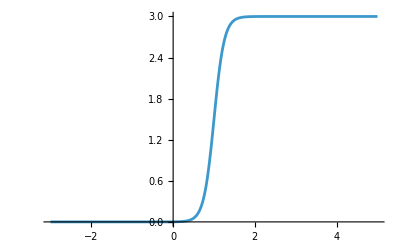

```mathematica
Plot[Sform'[t]/Sform[t]//.{H->3,Om->4,tstar->1},{t,-3,5}]
```

### Write out coefficients

```mathematica
(*---2. Variable names to unpack from struct---*)
variables={"Phi","S","Sdot","Phidot","A","PhiZ","SZ","SdotZ","PhidotZ","AZ","PhiZZ","SZZ","SdotZZ","PhidotZZ","AZZ","z","LN","t","X","p2","a4","DS0","DS1","DS2","DS3","DS4"};

(*---3. Field names and coefficient labels---*)
fields={"Phi","S","Sdot","Phidot","A"};
coeffLabels={"Coeff0","Coeff1","Coeff2","Src"};
```

```mathematica
makeJuliaFuncBdry[field_,label_,expr_,exprB_]:=Module[{fname},fname=field<>label;
"function "<>fname<>"(v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\n"<>"if z == 0 \n co = "<>ToJuliaForm[ToString[InputForm[exprB]]]
<>";\n else \n    co = "<>ToJuliaForm[ToString[InputForm[expr]]]<>";\nend\n\n
"<>"    return co\nend\n\n"];
```

```mathematica
(*---1. Julia-compatible symbolic conversion---*)
ToJuliaForm[expr_]:=Module[{s},s=ToString[expr//FortranForm];
s=StringReplace[s,{"Sin["->"sin(","Sinh["->"sinh(","Cos["->"cos(","Cosh["->"cosh(","Tan["->"tan(","Tanh["->"tanh(","Sech["->"sech(","Exp["->"exp(","Log["->"log(","Sqrt["->"sqrt(","Vfun["->"Vfun(","Derivative[1][Vfun]["->"DV(","]"->")","\""->"","**"->"^"}];
s];
```

```mathematica
cosmocoeffs={SCoeffs,SdotCoeffs,PhidotCoeffs,ACoeffs};
cosmocoeffsB={SCoeffsB,SdotCoeffsB,PhidotCoeffsB,ACoeffsB};
```

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/ODECoeffExpr_New.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

```mathematica
str
```

```mathematica
str=strStart;
For[ii = 0, ii<=6,ii++,
str=str<>"function DS"<>ToString[ii]<>"f(t)\n\n";
str=str<>"res = "<>ToString[Simplify[D[Sform[t],{t,ii}]]//ToJuliaForm]<>"; \n\n";
str=str<>"return res;\nend\n\n";
];
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/CosmoS0Expr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

## Time step

### General

```mathematica
Clear[S0]
```

```mathematica
stepeq=(Subscript[Φfun, d][r,t]-(D[Φfun[r,t],t]+1/2 Afun[r,t]D[Φfun[r,t],r]))//.D[replWithSub,t]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
solTimeStep=Solve[0==stepeq,  Derivative[0,1][PhiSub][z,t]][[1]]//Expand//Simplify;
```

We need ξ’[t] here. We get it by demanding that the apparent horizon stay in the same spot. To that end, we demand ∂_t Ṡ(z_AH,t)=0 and we take z_AH=1/2. This requires solving  0=1/2 A Ṡ'+2/3 S (Φ̇)^2-1/2 Ṡ A'.

```mathematica
solconstr=Solve[0==constrEq//.{Subscript[Sfun, dd][r,t]->(D[Subscript[Sfun, d][r,t],t]+1/2 Afun[r,t]D[Subscript[Sfun, d][r,t],r])},Derivative[0,1][Subscript[Sfun, d]][r,t]][[1]]//Simplify//Expand
```

{Sfun_d^(0,1)[r,t]→-2/3 Sfun[r,t] Φfun_d[r,t]^2+1/2 Sfun_d[r,t] Afun^(1,0)[r,t]-1/2 Afun[r,t] Sfun_d^(1,0)[r,t]}

```mathematica
Solve[0==Subscript[Sfun, d][r,t]//.replWithSub//.{S0->(1&)}//.RtoZ,ξ[t]]//.toODE//.{z->1/2}//Simplify
```

{{ξ[t]→-2-(√(2 M^2-3 SdotSub[1/2]))/(√6)},{ξ[t]→-2+(√(2 M^2-3 SdotSub[1/2]))/(√6)}}

```mathematica
XiPrimeExpr=(Derivative[0,1][Subscript[Sfun, d]][r,t]//.solconstr)+DConst (Subscript[Sfun, d][r,t]+SDotConst);
```

```mathematica
XiPrimeExprAH=XiPrimeExpr//.replWithSub//.RtoZ//Simplify;
```

```mathematica
solXiPrime=Solve[0==XiPrimeExprAH,ξ'[t]][[1]]//Expand//Simplify;
```

```mathematica
XiPrimeStr=ξ'[t]//.solXiPrime//.toODE//.replfun//.replDS0//ToJuliaForm;
```

```mathematica
DtPhiStr=Derivative[0,1][PhiSub][z,t]//.solTimeStep//.toODE//.replfun//.replDS0//.{ξ'[t]->XPrime}//ToJuliaForm;
```

```mathematica
DtPhiB=SeriesCoefficient[Derivative[0,1][PhiSub][z,t]//.solTimeStep//.toODE,{z,0,0}]//.{PhiSub[0]->Subscript[p, 2][t],PhidotSub[0]->-PhidotCoeffsB[[1]]/PhidotCoeffsB[[2]]}//Simplify
```

1/(12 S0[t]^3)(-6 M S0'[t]^3+4 S0[t]^3 (-3 M ξ[t]^3+3 (PhidotSub'[0]+2 PhiSub'[0])+ξ[t] (2 M^3+9 p_2[t]+6 M ξ'[t]))+3 M S0[t] S0'[t] (-5 ξ[t] S0'[t]+S0''[t])+3 M S0[t]^2 (7 ξ[t] S0''[t]+S0^(3)[t]))

```mathematica
DtPhiBStr=DtPhiB//.{PhidotSub'[0]->PhidotZ,PhiSub'[0]->PhiZ,ξ'[t]->XPrime}//.replfun//.replDS0//ToJuliaForm//ToString;
```

```mathematica
a4PrimeStr=Subscript[a, 4]'[t]//.sola4//.toODE//.replfun//.replDS0//.{ξ'[t]->XPrime,Subscript[p, 2]'[t]->p2Prime}//ToJuliaForm
```

```mathematica
str=strStart;
```

```mathematica
str=str<>"function DtX(v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\n";
str=str<>"XPrime = "<>ToString[XiPrimeStr]<>";\n\n return XPrime\nend\n\n";
```

```mathematica
str=str<>"function DtPhi(XPrime, v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\nif z == 0\n";
str=str<>"PhiT = "<>DtPhiBStr<>";\nelse\n"; 
str=str<>"PhiT = "<>ToString[DtPhiStr]<>";\nend\n\n return PhiT\nend\n\n";
```

```mathematica
str=str<>"function Dta4(params, DSvals, XPrime, p2Prime)\n\n t, X, p2, a4 = params;\n DS0, DS1, DS2, DS3, DS4 = DSvals;\n\n";
str= str<>"a4Prime = "<>ToString[a4PrimeStr]<>";\n\n";
str=str<>"return a4Prime;\nend;\n\n";
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/CosmoTimeStepExpr_New.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

```mathematica
str
```

# ==============================================
#  Auto-generated Julia code from Mathematica
#  Do not edit manually
# ==============================================


# ----------------------------------------------
#  Generated functions
# ----------------------------------------------

function DtX(v::PDEVars{T}) where {T}

    @unpack Phi, S, Sdot, Phidot, A, PhiZ, SZ, SdotZ, PhidotZ, AZ, PhiZZ, SZZ, SdotZZ, PhidotZZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

XPrime = (48*DS1^10*(199 - 90*LN)*LN^3*M^4*z^13 - 24*DS0*DS1^8*LN^3*M^4*z^12*(4*DS2*(338 + 45*LN)*z + 3*DS1*(399 - 90*LN + 2*(-599 + 90*LN)*X*z)) - 20*DS0^9*(3240*DS1 + 6480*DConst*DS1*z + 6480*DS2*z + 6480*DS1*X*z - 1080*DS1*M^2*z^2 + 6480*DConst*SDotConst*z^2 + 6480*DConst*DS1*X*z^2 + 6480*DS2*X*z^2 + 3240*DS1*X^2*z^2 - 1440*DConst*DS1*M^2*z^3 + 810*DS2*M^2*z^3 - 2880*DS1*M^2*X*z^3 - 9720*A*DS1*z^4 + 324*DS3*M^2*z^4 + 540*DConst*DS2*LN*M^2*z^4 + 540*DS3*LN*M^2*z^4 + 600*DS1*M^4*z^4 + 4320*DS1*M*Phidot*z^4 + 3240*SdotZ*z^4 - 720*DS1*M^2*X^2*z^4 - 3240*AZ*DS1*z^5 + 432*DConst*DS3*LN*M^2*z^5 - 180*DS2*M^4*z^5 - 900*DS2*LN*M^4*z^5 - 6480*DS2*LN*M*Phidot*z^5 - 6480*A*DS1*X*z^5 + 648*DS3*M^2*X*z^5 - 1080*DConst*DS2*LN*M^2*X*z^5 - 432*DS3*LN*M^2*X*z^5 + 6480*SdotZ*X*z^5 - 2430*DS2*M^2*X^2*z^5 + 4860*DS2*LN*M^2*X^2*z^5 + 720*A*DS1*M^2*z^6 - 36*DS3*M^4*z^6 - 756*DS3*LN*M^4*z^6 - 4320*DS3*LN*M*Phidot*z^6 - 480*DS1*M^3*Phidot*z^6 - 4320*DS1*Phidot^2*z^6 - 2160*M^2*SdotZ*z^6 - 3240*AZ*DS1*X*z^6 + 360*DS2*M^4*X*z^6 + 2700*DS2*LN*M^4*X*z^6 + 6480*DS2*LN*M*Phidot*X*z^6 + 324*DS3*M^2*X^2*z^6 - 972*DS3*LN*M^2*X^2*z^6 + 3240*SdotZ*X^2*z^6 - 1620*DS2*M^2*X^3*z^6 + 4860*DS2*LN*M^2*X^3*z^6 + 720*AZ*DS1*M^2*z^7 - 270*A*DS2*M^2*z^7 - 75*DS4*LN*M^4*z^7 - 112*DS2*LN*M^6*z^7 - 216*DS2*LN*M^3*p2*z^7 + 2880*DS2*LN*M^3*Phidot*z^7 + 1296*DS3*LN*M^4*X*z^7 - 4320*DS3*LN*M*Phidot*X*z^7 - 3024*DS2*LN*M^4*X^2*z^7 + 12960*DS2*LN*M*Phidot*X^2*z^7 - 216*A*DS3*M^2*z^8 - 270*AZ*DS2*LN*M^2*z^8 + 216*A*DS3*LN*M^2*z^8 + 2016*DS3*LN*M^3*Phidot*z^8 + 480*DS1*M^2*Phidot^2*z^8 + 3240*A*SdotZ*z^8 + 540*A*DS2*M^2*X*z^8 - 540*A*DS2*LN*M^2*X*z^8 - 8640*DS2*LN*M^3*Phidot*X*z^8 - 216*AZ*DS3*LN*M^2*z^9 + 300*DS4*LN*M^3*Phidot*z^9 + 448*DS2*LN*M^5*Phidot*z^9 + 864*DS2*LN*M^2*p2*Phidot*z^9 - 720*DS2*LN*M^2*Phidot^2*z^9 + 540*AZ*DS2*LN*M^2*X*z^9 - 3744*DS3*LN*M^3*Phidot*X*z^9 + 7776*DS2*LN*M^3*Phidot*X^2*z^9 - 576*DS3*LN*M^2*Phidot^2*z^10 + 2160*DS2*LN*M^2*Phidot^2*X*z^10 - 300*DS4*LN*M^2*Phidot^2*z^11 - 448*DS2*LN*M^4*Phidot^2*z^11 - 864*DS2*LN*M*p2*Phidot^2*z^11 + 2304*DS3*LN*M^2*Phidot^2*X*z^11 - 3456*DS2*LN*M^2*Phidot^2*X^2*z^11 - 1080*S*z^5*(M - 2*Phidot*z^2)^2 - 1080*Sdot*z^3*(-12 - 6*DConst*z - 18*X*z + 4*M^2*z^2 - 6*X^2*z^2 + 3*AZ*z^5)) + DS0^2*DS1^6*LN^3*M^3*z^11*(36*DS2^2*(1361 + 90*LN)*M*z^2 + DS1^2*(41373*M - 2430*LN*M + 108*(-1799 + 90*LN)*M*X*z + 7360*M^3*z^2 + 17280*p2*z^2 - 972*(-271 + 10*LN)*M*X^2*z^2) - 36*DS1*M*z*(-24*DS3*(2 + 5*LN)*z + 5*DS2*(-343 - 90*LN + 10*(107 + 18*LN)*X*z))) + 3600*DS0^10*(-18*DConst - 36*DConst*X*z + 6*DConst*M^2*z^2 - 18*DConst*X^2*z^2 - 2*M^4*z^3 + 9*AZ*z^4 + 2*M^4*X*z^4 + 18*AZ*X*z^5 - 3*AZ*M^2*z^6 + 9*AZ*X^2*z^6 - 6*A*z^3*(-6 - 9*X*z + M^2*z^2 - 3*X^2*z^2) - 8*M*Phidot*z^3*(3 - M^2*z^2 + X*z*(3 + M^2*z^2)) + 8*Phidot^2*z^5*(3 - M^2*z^2 + X*z*(3 + M^2*z^2))) + DS0^7*z^2*(64800*DS1^3 + 25200*DS1^3*M^2*z^2 - 32400*DS1^3*LN*M^2*z^2 + 37800*DS1^2*DS2*M^2*z^3 - 21600*DConst*DS1^3*LN*M^2*z^3 - 162000*DS1^2*DS2*LN*M^2*z^3 + 97200*DS1^2*DS2*LN^2*M^2*z^3 + 21600*DS1^3*M^2*X*z^3 + 129600*DS1^3*LN*M^2*X*z^3 + 38880*DS1*DS2^2*M^2*z^4 - 6480*DS1^2*DS3*M^2*z^4 - 116640*DS1*DS2^2*LN*M^2*z^4 + 19440*DS1^2*DS3*LN*M^2*z^4 + 113400*DS1*DS2^2*LN^2*M^2*z^4 + 64800*DS1^2*DS3*LN^2*M^2*z^4 - 7200*DS1^3*M^4*z^4 - 3600*DS1^3*LN*M^4*z^4 - 43200*DS1^3*LN*M*Phidot*z^4 - 64800*DS1^2*SdotZ*z^4 - 10800*DS1^2*DS2*M^2*X*z^4 + 32400*DS1^2*DS2*LN*M^2*X*z^4 - 291600*DS1^2*DS2*LN^2*M^2*X*z^4 + 10800*DS1^3*M^2*X^2*z^4 - 32400*DS1^3*LN*M^2*X^2*z^4 + 108000*DS1*DS2*DS3*LN^2*M^2*z^5 - 4800*DS1^2*DS2*M^4*z^5 + 8676*DS1^2*DS2*LN*M^4*z^5 - 56160*DS1^2*DS2*LN^2*M^4*z^5 + 86400*DS1^2*DS2*LN*M*Phidot*z^5 - 259200*DS1*DS2^2*LN^2*M^2*X*z^5 - 64800*DS1^2*DS3*LN^2*M^2*X*z^5 + 28800*DS1^3*LN*M^4*X*z^5 - 432000*DS1^3*LN*M*Phidot*X*z^5 + 10800*A*DS1^3*M^2*z^6 - 10800*A*DS1^3*LN*M^2*z^6 + 21600*DS1*DS3^2*LN^2*M^2*z^6 - 38160*DS1*DS2^2*LN^2*M^4*z^6 - 42840*DS1^2*DS3*LN^2*M^4*z^6 + 57600*DS1^3*LN*M^3*Phidot*z^6 - 86400*DS1*DS2*DS3*LN^2*M^2*X*z^6 + 270000*DS1^2*DS2*LN^2*M^4*X*z^6 + 64800*DS1*DS2^2*LN^2*M^2*X^2*z^6 - 129600*DS1^2*DS3*LN^2*M^2*X^2*z^6 + 388800*DS1^2*DS2*LN^2*M^2*X^3*z^6 + 10800*AZ*DS1^3*LN*M^2*z^7 - 17784*DS2^3*LN^2*M^4*z^7 - 45900*DS1*DS2*DS3*LN^2*M^4*z^7 - 4500*DS1^2*DS4*LN^2*M^4*z^7 + 11340*DS2^3*LN^3*M^4*z^7 - 12240*DS1^2*DS2*LN^2*M^6*z^7 - 25920*DS1^2*DS2*LN^2*M^3*p2*z^7 + 13296*DS1^2*DS2*LN*M^3*Phidot*z^7 + 51840*DS1^2*DS2*LN^2*M^3*Phidot*z^7 + 21600*DS1*DS2*LN*M^2*SdotZ*z^7 + 198720*DS1*DS2^2*LN^2*M^4*X*z^7 + 138240*DS1^2*DS3*LN^2*M^4*X*z^7 - 86400*DS1^3*LN*M^3*Phidot*X*z^7 - 492480*DS1^2*DS2*LN^2*M^4*X^2*z^7 - 11856*DS2^2*DS3*LN^2*M^4*z^8 - 8040*DS1*DS3^2*LN^2*M^4*z^8 - 3000*DS1*DS2*DS4*LN^2*M^4*z^8 + 19440*DS2^2*DS3*LN^3*M^4*z^8 - 4480*DS1*DS2^2*LN^2*M^6*z^8 - 3680*DS1^2*DS3*LN^2*M^6*z^8 - 8640*DS1*DS2^2*LN^2*M^3*p2*z^8 - 8640*DS1^2*DS3*LN^2*M^3*p2*z^8 + 44640*DS1*DS2^2*LN^2*M^3*Phidot*z^8 + 31680*DS1^2*DS3*LN^2*M^3*Phidot*z^8 - 14400*DS1^3*LN*M^2*Phidot^2*z^8 + 35568*DS2^3*LN^2*M^4*X*z^8 + 109080*DS1*DS2*DS3*LN^2*M^4*X*z^8 + 9000*DS1^2*DS4*LN^2*M^4*X*z^8 - 63180*DS2^3*LN^3*M^4*X*z^8 + 24480*DS1^2*DS2*LN^2*M^6*X*z^8 + 51840*DS1^2*DS2*LN^2*M^3*p2*X*z^8 - 216000*DS1^2*DS2*LN^2*M^3*Phidot*X*z^8 - 220320*DS1*DS2^2*LN^2*M^4*X^2*z^8 - 146880*DS1^2*DS3*LN^2*M^4*X^2*z^8 + 336960*DS1^2*DS2*LN^2*M^4*X^3*z^8 + 12240*DS2*DS3^2*LN^3*M^4*z^9 + 3375*DS2^2*DS4*LN^3*M^4*z^9 + 5040*DS2^3*LN^3*M^6*z^9 + 9720*DS2^3*LN^3*M^3*p2*z^9 + 35568*DS2^3*LN^2*M^3*Phidot*z^9 + 48600*DS1*DS2*DS3*LN^2*M^3*Phidot*z^9 + 9000*DS1^2*DS4*LN^2*M^3*Phidot*z^9 - 6480*DS2^3*LN^3*M^3*Phidot*z^9 + 24480*DS1^2*DS2*LN^2*M^5*Phidot*z^9 + 51840*DS1^2*DS2*LN^2*M^2*p2*Phidot*z^9 - 22896*DS1^2*DS2*LN*M^2*Phidot^2*z^9 - 8640*DS1^2*DS2*LN^2*M^2*Phidot^2*z^9 - 105840*DS2^2*DS3*LN^3*M^4*X*z^9 - 224640*DS1*DS2^2*LN^2*M^3*Phidot*X*z^9 - 146880*DS1^2*DS3*LN^2*M^3*Phidot*X*z^9 + 57600*DS1^3*LN*M^2*Phidot^2*X*z^9 + 168480*DS2^3*LN^3*M^4*X^2*z^9 + 466560*DS1^2*DS2*LN^2*M^3*Phidot*X^2*z^9 + 2880*DS3^3*LN^3*M^4*z^10 + 4500*DS2*DS3*DS4*LN^3*M^4*z^10 + 6720*DS2^2*DS3*LN^3*M^6*z^10 + 12960*DS2^2*DS3*LN^3*M^3*p2*z^10 + 23712*DS2^2*DS3*LN^2*M^3*Phidot*z^10 + 11280*DS1*DS3^2*LN^2*M^3*Phidot*z^10 + 6000*DS1*DS2*DS4*LN^2*M^3*Phidot*z^10 - 4320*DS2^2*DS3*LN^3*M^3*Phidot*z^10 + 8960*DS1*DS2^2*LN^2*M^5*Phidot*z^10 + 7360*DS1^2*DS3*LN^2*M^5*Phidot*z^10 + 17280*DS1*DS2^2*LN^2*M^2*p2*Phidot*z^10 + 17280*DS1^2*DS3*LN^2*M^2*p2*Phidot*z^10 - 62640*DS2*DS3^2*LN^3*M^4*X*z^10 - 13500*DS2^2*DS4*LN^3*M^4*X*z^10 - 20160*DS2^3*LN^3*M^6*X*z^10 - 38880*DS2^3*LN^3*M^3*p2*X*z^10 - 71136*DS2^3*LN^2*M^3*Phidot*X*z^10 - 160560*DS1*DS2*DS3*LN^2*M^3*Phidot*X*z^10 - 18000*DS1^2*DS4*LN^2*M^3*Phidot*X*z^10 + 12960*DS2^3*LN^3*M^3*Phidot*X*z^10 - 48960*DS1^2*DS2*LN^2*M^5*Phidot*X*z^10 - 103680*DS1^2*DS2*LN^2*M^2*p2*Phidot*X*z^10 + 246240*DS2^2*DS3*LN^3*M^4*X^2*z^10 + 311040*DS1*DS2^2*LN^2*M^3*Phidot*X^2*z^10 + 207360*DS1^2*DS3*LN^2*M^3*Phidot*X^2*z^10 - 252720*DS2^3*LN^3*M^4*X^3*z^10 - 414720*DS1^2*DS2*LN^2*M^3*Phidot*X^3*z^10 + 1500*DS3^2*DS4*LN^3*M^4*z^11 + 2240*DS2*DS3^2*LN^3*M^6*z^11 + 4320*DS2*DS3^2*LN^3*M^3*p2*z^11 - 11520*DS3^3*LN^3*M^4*X*z^11 - 9000*DS2*DS3*DS4*LN^3*M^4*X*z^11 - 13440*DS2^2*DS3*LN^3*M^6*X*z^11 - 25920*DS2^2*DS3*LN^3*M^3*p2*X*z^11 + 86400*DS2*DS3^2*LN^3*M^4*X^2*z^11 + 13500*DS2^2*DS4*LN^3*M^4*X^2*z^11 + 20160*DS2^3*LN^3*M^6*X^2*z^11 + 38880*DS2^3*LN^3*M^3*p2*X^2*z^11 - 207360*DS2^2*DS3*LN^3*M^4*X^3*z^11 + 155520*DS2^3*LN^3*M^4*X^4*z^11 - 21600*DS1*Sdot*z^3*(6*DS1 + DS2*(-1 + LN)*M^2*z^3) + 5400*LN*M*S*z^5*(-8*DS1*DS2*z*(M - 2*Phidot*z^2) + 12*DS1^2*(-1 + 2*X*z)*(M - 2*Phidot*z^2) + LN*M*z^2*(2*DS3*z + DS2*(3 - 6*X*z))^2)) + DS0^3*DS1^4*LN^2*M^2*z^8*(86400*DS1^2*S*z^3 + 12*DS2^3*LN*(-2453 + 180*LN)*M^2*z^5 - 24*DS1*DS2*LN*M^2*z^4*(-(DS3*(683 + 270*LN)*z) + 9*DS2*(162 - 45*LN + 2*(-272 + 45*LN)*X*z)) + 12*DS1^3*(7200 - 4*M^2*z^2 - 2835*LN*M^2*z^2 - 920*LN*M^4*z^4 - 2160*LN*M*p2*z^4 + 8*(-199 + 90*LN)*M*Phidot*z^4 - 32940*LN*M^2*X^2*z^4 + 28080*LN*M^2*X^3*z^5 + 80*LN*M*X*z^3*(180*M + 23*M^3*z^2 + 54*p2*z^2)) + DS1^2*LN*M^2*z^3*(DS2*(-21573 - 9720*LN + 108*(1159 + 360*LN)*X*z + 1600*M^2*z^2 - 108*(1519 + 360*LN)*X^2*z^2) + 12*z*(500*DS4*z + 3*DS3*(449 - 90*LN + 2*(-1169 + 90*LN)*X*z)))) + DS0^4*DS1^2*LN^2*M^2*z^7*(24*DS2^4*(247 - 45*LN)*LN*M^2*z^6 + 43200*DS1^2*S*z^3*(-2*DS2*z + DS1*(-3 + 6*X*z)) + 12*DS1*DS2^2*LN*M^2*z^5*(-2695*DS3*z + 3*DS2*(-831 - 90*LN + 2*(691 + 90*LN)*X*z)) - DS1^2*LN*M*z^4*(36*DS3^2*(247 + 30*LN)*M*z^2 + DS2^2*(43767*M + 14580*LN*M - 324*(667 + 180*LN)*M*X*z + 7120*M^3*z^2 + 12960*p2*z^2 + 324*(887 + 180*LN)*M*X^2*z^2) - 12*DS2*M*z*(-500*DS4*z + 81*DS3*(-59 - 10*LN + 2*(99 + 10*LN)*X*z))) + 36*DS1^4*(-1200 - 999*M^2*z^2 + 315*LN*M^2*z^2 + 115*LN*M^4*z^4 + 270*LN*M*p2*z^4 - 7020*LN*M^2*X^3*z^5 + 4320*LN*M^2*X^4*z^6 + 2*M*Phidot*z^4*(599 - 90*LN + 18*(-111 + 10*LN)*X*z) + 20*LN*M*X^2*z^4*(234*M + 23*M^3*z^2 + 54*p2*z^2) + X*(-1080*LN*M*p2*z^5 - 5*LN*M^2*z^3*(351 + 92*M^2*z^2) + 6*z*(1600 + 333*M^2*z^2))) + DS1^3*(12*DS2*z*(-7200 - 1506*M^2*z^2 - 3645*LN*M^2*z^2 - 1580*LN*M^4*z^4 - 3240*LN*M*p2*z^4 + 4*(1153 + 270*LN)*M*Phidot*z^4 - 37260*LN*M^2*X^2*z^4 + 32400*LN*M^2*X^3*z^5 + 20*LN*M*X*z^3*(837*M + 158*M^3*z^2 + 324*p2*z^2)) - 5*LN*M*z^4*(1800*DS4*M*z*(1 - 2*X*z) + DS3*(7227*M - 37260*M*X*z + 1472*M^3*z^2 + 3456*p2*z^2 + 53676*M*X^2*z^2)))) - 4*DS0^8*z^2*(10*DS1^2*(1620*DConst + 405*M^2*z - 810*DConst*LN*M^2*z^2 - 270*M^4*z^3 - 90*LN*M^4*z^3 + 1620*DConst*LN*M^2*X*z^3 - 1215*M^2*X^2*z^3 + 2430*LN*M^2*X^2*z^3 - 810*AZ*z^4 + 540*M^4*X*z^4 + 270*LN*M^4*X*z^4 - 810*M^2*X^3*z^4 + 2430*LN*M^2*X^3*z^4 - 46*LN*M^6*z^5 - 108*LN*M^3*p2*z^5 - 1512*LN*M^4*X^2*z^5 + 405*AZ*LN*M^2*z^6 - 810*AZ*LN*M^2*X*z^7 - 8*LN*M*Phidot^2*z^7*(45*M - 135*M*X*z + 23*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) + 405*A*z^3*(-4 + M^2*z^2 + 2*(-1 + LN)*M^2*X*z^3) + 8*LN*M*Phidot*z^3*(-405 + 180*M^2*z^2 + 23*M^4*z^4 + 54*M*p2*z^4 + 162*X^2*z^2*(5 + 3*M^2*z^2) - 135*X*z*(-3 + 4*M^2*z^2))) + z^3*(2700*DS2^2*M^2 - 5400*DS2^2*LN*M^2 - 12150*DS2^2*LN^2*M^2 + 2160*DS2*DS3*M^2*z - 6480*DS2*DS3*LN*M^2*z - 16200*DS2*DS3*LN^2*M^2*z - 32400*DS2*SdotZ*z - 5400*DS2^2*M^2*X*z + 16200*DS2^2*LN*M^2*X*z + 36450*DS2^2*LN^2*M^2*X*z - 5400*DS3^2*LN^2*M^2*z^2 - 1482*DS2^2*LN*M^4*z^2 + 7020*DS2^2*LN^2*M^4*z^2 + 16200*DS2*DS3*LN^2*M^2*X*z^2 + 9630*DS2*DS3*LN^2*M^4*z^3 + 10800*DS2*LN*M^2*SdotZ*z^3 - 5400*DS3^2*LN^2*M^2*X*z^3 - 33750*DS2^2*LN^2*M^4*X*z^3 + 32400*DS2*DS3*LN^2*M^2*X^2*z^3 - 48600*DS2^2*LN^2*M^2*X^3*z^3 + 3240*DS3^2*LN^2*M^4*z^4 + 1125*DS2*DS4*LN^2*M^4*z^4 + 1680*DS2^2*LN^2*M^6*z^4 + 3240*DS2^2*LN^2*M^3*p2*z^4 + 5928*DS2^2*LN*M^3*Phidot*z^4 - 6480*DS2^2*LN^2*M^3*Phidot*z^4 + 5400*DS3*LN*M^2*SdotZ*z^4 - 34560*DS2*DS3*LN^2*M^4*X*z^4 - 21600*DS2*LN*M^2*SdotZ*X*z^4 + 61560*DS2^2*LN^2*M^4*X^2*z^4 + 750*DS3*DS4*LN^2*M^4*z^5 + 1120*DS2*DS3*LN^2*M^6*z^5 + 2160*DS2*DS3*LN^2*M^3*p2*z^5 - 7920*DS2*DS3*LN^2*M^3*Phidot*z^5 - 7560*DS3^2*LN^2*M^4*X*z^5 - 2250*DS2*DS4*LN^2*M^4*X*z^5 - 3360*DS2^2*LN^2*M^6*X*z^5 - 6480*DS2^2*LN^2*M^3*p2*X*z^5 + 27000*DS2^2*LN^2*M^3*Phidot*X*z^5 + 36720*DS2*DS3*LN^2*M^4*X^2*z^5 - 42120*DS2^2*LN^2*M^4*X^3*z^5 - 2880*DS3^2*LN^2*M^3*Phidot*z^6 - 2250*DS2*DS4*LN^2*M^3*Phidot*z^6 - 3360*DS2^2*LN^2*M^5*Phidot*z^6 - 6480*DS2^2*LN^2*M^2*p2*Phidot*z^6 - 5928*DS2^2*LN*M^2*Phidot^2*z^6 + 1080*DS2^2*LN^2*M^2*Phidot^2*z^6 + 36720*DS2*DS3*LN^2*M^3*Phidot*X*z^6 - 58320*DS2^2*LN^2*M^3*Phidot*X^2*z^6 - 1500*DS3*DS4*LN^2*M^3*Phidot*z^7 - 2240*DS2*DS3*LN^2*M^5*Phidot*z^7 - 4320*DS2*DS3*LN^2*M^2*p2*Phidot*z^7 + 11520*DS3^2*LN^2*M^3*Phidot*X*z^7 + 4500*DS2*DS4*LN^2*M^3*Phidot*X*z^7 + 6720*DS2^2*LN^2*M^5*Phidot*X*z^7 + 12960*DS2^2*LN^2*M^2*p2*Phidot*X*z^7 - 51840*DS2*DS3*LN^2*M^3*Phidot*X^2*z^7 + 51840*DS2^2*LN^2*M^3*Phidot*X^3*z^7 - 5400*LN*M*S*z^2*(M - 2*Phidot*z^2)*(-2*DS3*z + DS2*(-3 + 6*X*z)) + 5400*Sdot*(-(DS3*(-1 + LN)*M^2*z^3) + 2*DS2*(-6 + M^2*z^2 + 2*(-1 + LN)*M^2*X*z^3))) + 15*DS1*(4*DS2*(540 + 336*M^2*z^2 - 270*LN*M^2*z^2 - 162*DConst*LN*M^2*z^3 - 108*M^2*X*z^3 + 432*LN*M^2*X*z^3 - 79*M^4*z^4 + 46*LN*M^4*z^4 - 324*M^2*X^2*z^4 + 972*LN*M^2*X^2*z^4 + 80*M^4*X*z^5 + 44*LN*M^4*X*z^5 - 81*A*(-1 + LN)*M^2*z^6 + 81*AZ*LN*M^2*z^7 + 84*LN*M^2*Phidot^2*z^8*(-1 + 4*X*z) - 12*LN*M*Phidot*z^4*(75 - 22*M^2*z^2 + 12*X*z*(-5 + 4*M^2*z^2))) + DS3*M*z^3*(-188*LN*M*Phidot^2*z^6 + 12*LN*Phidot*z^2*(-120 + 29*M^2*z^2) + M*(360 - 360*(-1 + 3*LN)*X*z - 80*M^2*z^2 + LN*(-720 + 33*M^2*z^2))))) + DS0^5*DS1*M^2*z^6*(24*DS2^3*LN^3*(-247 + 45*LN)*M^2*z^6*(-2*DS3*z + DS2*(-3 + 6*X*z)) + 40*DS1^4*(270 - 810*LN - 2025*LN^2 + 1575*LN^2*M^2*z^2 + 184*LN^2*M^4*z^4 + 432*LN^2*M*p2*z^4 - 540*LN^2*X*z*(3 + 10*M^2*z^2) + 324*LN^2*X^2*z^2*(35 + 17*M^2*z^2) - 4*LN^2*Phidot*z^4*(315*M - 1350*M*X*z + 92*M^3*z^2 + 216*p2*z^2 + 1944*M*X^2*z^2)) + 5400*DS1*LN^2*S*z^3*(4*DS2^2*z^2 + 9*DS1^2*(1 - 2*X*z)^2 + 4*DS1*z*(-4*DS3*z + DS2*(-3 + 6*X*z))) + DS1*DS2*LN^3*M*z^5*(-12*DS3^2*(7 + 180*LN)*M*z^2 + DS2^2*(32517*M - 9720*LN*M + 108*(-1451 + 360*LN)*M*X*z + 2240*M^3*z^2 + 4320*p2*z^2 - 972*(-199 + 40*LN)*M*X^2*z^2) + 12*DS2*M*z*(125*DS4*z + 54*DS3*(34 - 15*LN + 6*(-18 + 5*LN)*X*z))) + 30*DS1^2*LN^2*z^2*(2*DS3*LN*M^2*z^4*(-100*DS4*z + 3*DS3*(-37 + 242*X*z)) + 2*DS2^2*(360 + 546*M^2*z^2 + 243*LN*M^2*z^2 - 20*LN*M^4*z^4 - 1172*M*Phidot*z^4 + 4860*LN*M^2*X^2*z^4 - 3888*LN*M^2*X^3*z^5 + 8*LN*M^2*X*z^3*(-243 + 5*M^2*z^2)) - DS2*LN*M*z^3*(150*DS4*M*z*(1 - 2*X*z) + DS3*(-39*M + 108*M*X*z + 176*M^3*z^2 + 288*p2*z^2 + 612*M*X^2*z^2))) + 3*DS1^3*LN^2*z*(1125*DS4*LN*M^2*z^4*(1 - 2*X*z)^2 - 8*DS3*z*(3600 - 671*M^2*z^2 - 810*LN*M^2*z^2 - 230*LN*M^4*z^4 - 540*LN*M*p2*z^4 + 2*(271 + 90*LN)*M*Phidot*z^4 - 10260*LN*M^2*X^2*z^4 + 8640*LN*M^2*X^3*z^5 + 10*LN*M*X*z^3*(441*M + 46*M^3*z^2 + 108*p2*z^2)) + 12*DS2*(-4200 + 2038*M^2*z^2 + 945*LN*M^2*z^2 + 370*LN*M^4*z^4 + 810*LN*M*p2*z^4 - 21060*LN*M^2*X^3*z^5 + 12960*LN*M^2*X^4*z^6 + 4*M*Phidot*z^4*(-3*(173 + 45*LN) + 2*(899 + 135*LN)*X*z) + 40*LN*M*X^2*z^4*(351*M + 37*M^3*z^2 + 81*p2*z^2) - X*z*(-1200 + 4796*M^2*z^2 + 3240*LN*M*p2*z^4 + 5*LN*M^2*z^2*(1053 + 296*M^2*z^2))))) + DS0^6*M*z^5*(-6*DS2^2*LN^3*(-247 + 45*LN)*M^3*z^6*(2*DS3*z + DS2*(3 - 6*X*z))^2 + 10800*DS1*LN*S*z^3*(8*DS1^2*(M - 2*Phidot*z^2) + 2*DS2*LN*M*z^2*(2*DS3*z + DS2*(3 - 6*X*z)) + 3*DS1*LN*M*z*(-1 + 2*X*z)*(-2*DS3*z + DS2*(-3 + 6*X*z))) + DS1*LN^2*M^2*z^5*(2820*DS3^3*LN*M*z^3 - 60*DS2*DS3*LN*M*z^2*(-50*DS4*z + 3*DS3*(-107 + 334*X*z)) - 12*DS2^3*(988*M - 2025*LN*M - 560*LN*M^3*z^2 - 1080*LN*p2*z^2 + 8*(-247 + 45*LN)*Phidot*z^2 - 28620*LN*M*X^2*z^2 + 23760*LN*M*X^3*z^3 + 20*LN*X*z*(603*M + 56*M^3*z^2 + 108*p2*z^2)) + 5*DS2^2*LN*z*(900*DS4*M*z*(1 - 2*X*z) + DS3*(7461*M - 37908*M*X*z + 896*M^3*z^2 + 1728*p2*z^2 + 50004*M*X^2*z^2))) + 60*DS1^3*M*z*(2*DS2*(-252 + 756*LN + 270*LN^2 + 99*LN^2*M^2*z^2 + 4320*LN^2*X^2*z^2 + 44*LN^2*M^4*z^4 + 72*LN^2*M*p2*z^4 - 36*LN^2*X*z*(75 + 4*M^2*z^2) - 8*LN^2*Phidot*z^4*(6*M + 9*M*X*z + 11*M^3*z^2 + 18*p2*z^2)) + LN^2*z*(100*DS4*M*z^3*(M - 2*Phidot*z^2) - 3*DS3*(120 - 177*M^2*z^2 + 2*M*Phidot*z^4*(57 - 322*X*z) + 6*X*z*(200 + 67*M^2*z^2)))) + 12*DS1^4*(4*(199 - 90*LN)*LN*M*Phidot^2*z^6 - 4*LN*Phidot*z^2*(3600 - 201*M^2*z^2 - 540*LN*M^2*z^2 - 230*LN*M^4*z^4 - 540*LN*M*p2*z^4 - 4860*LN*M^2*X^2*z^4 + 4320*LN*M^2*X^3*z^5 + 10*LN*M*X*z^3*(225*M + 46*M^3*z^2 + 108*p2*z^2)) + M*(-1350 + 9900*LN + 4050*LN^2 - 601*LN*M^2*z^2 - 2340*LN^2*M^2*z^2 - 460*LN^2*M^4*z^4 - 1080*LN^2*M*p2*z^4 - 20520*LN^2*M^2*X^2*z^4 + 1080*LN^2*X^3*z^3*(15 + 13*M^2*z^2) + 10*X*z*(270 - 810*LN + 216*LN^2*M*p2*z^4 + LN^2*(-1215 + 1125*M^2*z^2 + 92*M^4*z^4)))) + 2*DS1^2*LN^2*M*z^2*(10*DS3*LN*M*z^4*(225*DS4*M*z*(1 - 2*X*z) + 4*DS3*(153*M - 783*M*X*z + 23*M^3*z^2 + 54*p2*z^2 + 1080*M*X^2*z^2)) + 18*DS2^2*(2400 - 697*M^2*z^2 + 945*LN*M^2*z^2 + 395*LN*M^4*z^4 + 810*LN*M*p2*z^4 - 21060*LN*M^2*X^3*z^5 + 12960*LN*M^2*X^4*z^6 + 2*M*Phidot*z^4*(297 - 270*LN + 2*(-577 + 270*LN)*X*z) + 20*LN*M*X^2*z^4*(702*M + 79*M^3*z^2 + 162*p2*z^2) - X*z*(3000 - 1754*M^2*z^2 + 3240*LN*M*p2*z^4 + 5*LN*M^2*z^2*(1053 + 316*M^2*z^2))) - 3*DS2*(-1125*DS4*LN*M^2*z^4*(1 - 2*X*z)^2 + 8*DS3*(2*(121 + 90*LN)*M*Phidot*z^5 + 3*z*(-300 - 7*M^2*z^2 - 270*LN*M^2*z^2 - 85*LN*M^4*z^4 - 180*LN*M*p2*z^4 - 3420*LN*M^2*X^2*z^4 + 2880*LN*M^2*X^3*z^5 + 10*LN*M*X*z^3*(147*M + 17*M^3*z^2 + 36*p2*z^2)))))))/(720*DS0^7*z*(30*DS1^3*(1 - 3*LN)*M^2*z^5 + 180*DS0^3*(1 + X*z) - 9*DS0*DS1*M^2*z^4*(6*DS2*(1 - 3*LN)*z + 5*DS1*(1 - 2*LN + 2*(-1 + 3*LN)*X*z)) + DS0^2*(-360*Sdot*z^4 + 20*DS1*z*(9 + 2*M^2*z^2) + 3*z^4*(4*(DS3*(1 - 3*LN)*M^2 - 15*SdotZ)*z + 5*DS2*M^2*(1 - 2*LN + 2*(-1 + 3*LN)*X*z)))));

 return XPrime
end

function DtPhi(XPrime, v::PDEVars{T}) where {T}

    @unpack Phi, S, Sdot, Phidot, A, PhiZ, SZ, SdotZ, PhidotZ, AZ, PhiZZ, SZZ, SdotZZ, PhidotZZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

if z == 0
PhiT = (-6*DS1^3*M + 3*DS0*DS1*M*(DS2 - 5*DS1*X) + 3*DS0^2*M*(DS3 + 7*DS2*X) + 4*DS0^3*(3*(PhidotZ + 2*PhiZ) - 3*M*X^3 + X*(2*M^3 + 9*p2 + 6*M*XPrime)))/(12*DS0^3);
else
PhiT = (-2*DS1^4*(-1 + 4*LN)*M*z^3*(-3*DS1 + DS2*LN*M^2*z^3) + 2*DS0^5*(-2*M^3 + 9*Phi + 6*Phidot - 9*M*X^2 + 3*PhiZ*z + 4*M^3*X*z + 18*Phi*X*z - 6*M*X^3*z + 12*M*X*XPrime*z - 6*M^2*Phi*z^2 + 6*PhiZ*X*z^2 + 9*Phi*X^2*z^2 - 18*Phi*XPrime*z^2 - 2*M^2*PhiZ*z^3 + 3*PhiZ*X^2*z^3 - 6*PhiZ*XPrime*z^3 + 3*A*z^2*(M - 2*M*X*z + 3*Phi*z^2 + PhiZ*z^3)) + DS0^4*(DS2*(-9*M + 21*M*X*z - 2*M^3*z^2 + 10*LN*M^3*z^2 - 15*M*X^2*z^2 + 63*LN*M*X^2*z^2 - 6*M*XPrime*z^2 - 12*PhiZ*z^3 + 6*M^3*X*z^3 - 40*LN*M^3*X*z^3 - 9*M*X^3*z^3 + 36*LN*M*X^3*z^3 + 18*M*X*XPrime*z^3 - 72*LN*M*X*XPrime*z^3 + 16*LN*M^3*X^2*z^4 + 4*LN*M^2*PhiZ*z^5 - 8*LN*M^2*PhiZ*X*z^6 + 3*A*M*z^4*(1 - 3*LN + 3*(-1 + 4*LN)*X*z) - 12*Phi*z^2*(3 - LN*M^2*z^2 + 2*LN*M^2*X*z^3)) + M*z*(6*DS4*LN*z + DS3*(3 + 6*X*z - 42*LN*X*z - 2*M^2*z^2 + 10*LN*M^2*z^2 + 3*X^2*z^2 - 12*LN*X^2*z^2 - 6*XPrime*z^2 + 24*LN*XPrime*z^2 - 4*LN*M^2*X*z^3 + 3*A*(1 - 4*LN)*z^4 + 6*LN*M*Phi*z^4 + 2*LN*M*PhiZ*z^5))) + DS0*DS1^2*M*z^2*(DS2^2*LN*(-1 + 4*LN)*M^2*z^4 + 3*DS1^2*(1 + 9*LN + 3*(-1 + 4*LN)*X*z) + DS1*(2*DS3*LN*(-1 + 4*LN)*M^2*z^4 + DS2*z*(15 + 19*LN^2*M^2*z^2 + 11*(1 - 4*LN)*LN*M^2*X*z^3 - 5*LN*(12 + M^2*z^2)))) - DS0^2*DS1*M*z*(2*DS1^2*(3 + 6*(1 - 7*LN)*X*z - 2*M^2*z^2 + 8*LN*M^2*z^2 + 3*(1 - 4*LN)*X^2*z^2 - 6*XPrime*z^2 + 24*LN*XPrime*z^2 + 3*A*(1 - 4*LN)*z^4) + DS2^2*z^2*(6 + 5*LN^2*M^2*z^2 + (1 - 4*LN)*LN*M^2*X*z^3 - LN*(24 + M^2*z^2)) + DS1*z*(DS3*z*(-3 + 3*LN^2*M^2*z^2 + 3*(1 - 4*LN)*LN*M^2*X*z^3 + LN*(12 - M^2*z^2)) + DS2*(3 + 6*LN^2*M^2*z^2 + 12*LN*(-1 + 4*LN)*M^2*X^2*z^4 + LN*(39 - 2*M^2*z^2) + X*z*(-9 - 36*LN^2*M^2*z^2 + 2*LN*(18 + 5*M^2*z^2))))) + DS0^3*(DS1*DS2*M*z*(3 + 6*X*z - 42*LN*X*z - 2*M^2*z^2 + 6*LN*M^2*z^2 + 3*X^2*z^2 - 12*LN*X^2*z^2 - 6*XPrime*z^2 + 24*LN*XPrime*z^2 + 4*LN*M^2*X*z^3 + 3*A*(1 - 4*LN)*z^4 - 6*LN*M*Phi*z^4 - 2*LN*M*PhiZ*z^5) + DS1^2*(9*M - 15*M*X*z - 2*M^3*z^2 + 6*LN*M^3*z^2 + 18*Phi*z^2 - 15*M*X^2*z^2 + 63*LN*M*X^2*z^2 - 6*M*XPrime*z^2 + 6*PhiZ*z^3 + 6*M^3*X*z^3 - 24*LN*M^3*X*z^3 - 9*M*X^3*z^3 + 36*LN*M*X^3*z^3 + 18*M*X*XPrime*z^3 - 72*LN*M*X*XPrime*z^3 + 3*A*M*z^4*(1 - 3*LN + 3*(-1 + 4*LN)*X*z)) + M*z^2*(DS3^2*(1 - 4*LN)*LN*M^2*z^4 + DS2*DS3*z*(-6 - 11*LN^2*M^2*z^2 + 7*LN*(-1 + 4*LN)*M^2*X*z^3 + 3*LN*(8 + M^2*z^2)) - 2*DS2^2*(3 + 3*LN^2*M^2*z^2 + 6*LN*(-1 + 4*LN)*M^2*X^2*z^4 - LN*(12 + M^2*z^2) + X*z*(-9 - 18*LN^2*M^2*z^2 + LN*(36 + 5*M^2*z^2))))))/(12*DS0^5*z);
end

 return PhiT
end

function Dta4(params, DSvals, XPrime, p2Prime)

 t, X, p2, a4 = params;
 DS0, DS1, DS2, DS3, DS4 = DSvals;

a4Prime = (2*((9*DS1*DS2*M^2)/DS0^2 + (2*(6*DS3*M^2 + DS1*(-27*a4 + 4*M^4 - 18*M*p2)))/DS0 - 18*M*p2Prime + (36*DS1*M^2*X^2)/DS0 + 36*M^2*X*XPrime))/27;

return a4Prime;
end;

## Constraint equation

```mathematica
Clear[Vfun]
```

```mathematica
constrEq
```

Sfun_dd[r,t]+2/3 Sfun[r,t] Φfun_d[r,t]^2-1/2 Sfun_d[r,t] Afun^(1,0)[r,t]

```mathematica
constrEqTmp=constrEq//.{Subscript[Sfun, dd][r,t]->(D[Subscript[Sfun, d][r,t],t]+1/2 Afun[r,t]D[Subscript[Sfun, d][r,t],r])}
```

2/3 Sfun[r,t] Φfun_d[r,t]^2+Sfun_d^(0,1)[r,t]-1/2 Sfun_d[r,t] Afun^(1,0)[r,t]+1/2 Afun[r,t] Sfun_d^(1,0)[r,t]

```mathematica
evolEqs
```

{2/3 Sfun[r,t] (Φfun^(1,0)[r,t])^2+Sfun^(2,0)[r,t],2/3 Sfun[r,t] Vfun[Φfun[r,t]]+(2 Sfun_d[r,t] Sfun^(1,0)[r,t])/Sfun[r,t]+Sfun_d^(1,0)[r,t],-1/2 Vfun'[Φfun[r,t]]+(3 Φfun_d[r,t] Sfun^(1,0)[r,t])/(2 Sfun[r,t])+(3 Sfun_d[r,t] Φfun^(1,0)[r,t])/(2 Sfun[r,t])+Φfun_d^(1,0)[r,t],-4/3 Vfun[Φfun[r,t]]-(12 Sfun_d[r,t] Sfun^(1,0)[r,t])/Sfun[r,t]^2+4 Φfun_d[r,t] Φfun^(1,0)[r,t]+Afun^(2,0)[r,t]}

```mathematica
replDtSdot={DtSdot[r,t]->D[(((r^2 Subscript[sd, 0][t]+r Subscript[sd, 1][t]+Subscript[sd, 2][t]+(Subscript[sd, 3][t])/r)+((Log[r] Subscript[σd1, 4][t])/r^2+(Log[r] Subscript[σd1, 5][t])/r^3(*+(Log[r] Subscript[σd1, 6][t])/r^4*)))/.PSDotSol),t]+DtSdotSub[r,t]/r^2}//Simplify;
```

```mathematica
DtSdotEq=D[evolEqs[[2]],t]//.{Derivative[0,1][Subscript[Sfun, d]][r,t] ->DtSdot[r,t],Derivative[1,1][Subscript[Sfun, d]][r,t]->Derivative[1,0][DtSdot][r,t] }//.Join[replDt,replDrDt]//Simplify
```

1/(3 Sfun[r,t]^2)(3 Sfun_d[r,t] Sfun^(1,0)[r,t] (-2 Sfun_d[r,t]+Afun[r,t] Sfun^(1,0)[r,t])+Sfun[r,t]^2 (3 DtSdot^(1,0)[r,t]+Vfun[Φfun[r,t]] (2 Sfun_d[r,t]-Afun[r,t] Sfun^(1,0)[r,t]))+Sfun[r,t]^3 Vfun'[Φfun[r,t]] (2 Φfun_d[r,t]-Afun[r,t] Φfun^(1,0)[r,t])+Sfun[r,t] (6 DtSdot[r,t] Sfun^(1,0)[r,t]-3 Sfun_d[r,t] (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]-2 Sfun_d^(1,0)[r,t]+Afun[r,t] Sfun^(2,0)[r,t])))

```mathematica
simpDtSdotEq=DtSdotEq//.replWithSub//.Join[replDtSdot,D[replDtSdot,r]]//Simplify;
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
simpDtSdotEq2=Simplify[-z^-1 simpDtSdotEq//.RtoZ//.toODE];
```

```mathematica
DtSdotCoeffs=Reverse[{Coefficient[simpDtSdotEq2,DtSdotSub'[z]],Coefficient[simpDtSdotEq2,DtSdotSub[z]],simpDtSdotEq2//.{DtSdotSub-> (0&)}}]//Simplify;
```

```mathematica
Simplify[simpDtSdotEq2-DtSdotCoeffs.{1,DtSdotSub[z],DtSdotSub'[z]}]
```

0

```mathematica
Clear[Vfun]
```

```mathematica
AppendTo[DtSdotCoeffs,0];
```

```mathematica
(*Put[SdotCoeffs,"sdotcoeffs.txt"]*)
```

```mathematica
Vfun[x_]:=Evaluate[-4/3 W[x]^2+1/2 W'[x]^2];
```

```mathematica
DtSdotCoeffsB={D[sdotbdry,t],1,0,0}//Simplify;
```

```mathematica
DtSdotCoeffsB//.replDS0
```

{(-27 DS1^3 M^2+54 DS0 DS1 DS2 M^2+DS0^2 (M^2 (-61 DS3+32 DS2 ξ[t])+DS1 (-72 M^2 ξ[t]^2+72 a_4[t]+4 M (-5 M^3+18 p_2[t]+8 M ξ'[t])))-72 DS0^3 (2 M^2 ξ[t] ξ'[t]-a_4'[t]-M p_2'[t]))/(144 DS0^2),1,0,0}

```mathematica
(*DtSdotCoeffsB=SeriesCoefficient[Simplify[DtSdotCoeffs//.{Log[1/z]->0}],{z,0,0}]*)
```

```mathematica
(*Series[Simplify[DtSdotCoeffs[[2]]//.{Log[1/z]->0}],{z,0,0}]*)
```

6 S0[t] (S0[t] ξ[t]+S0'[t])+O[z]^1

```mathematica
(*Series[Simplify[DtSdotCoeffs[[3]]//.{Log[1/z]->0}],{z,0,0}]*)
```

3 S0[t]^2+O[z]^1

```mathematica
(*Series[Simplify[DtSdotCoeffs[[1]]//.{Log[1/z]->0}],{z,0,0}]*)
```

```mathematica
(*AppendTo[DtSdotCoeffsB,0];*)
```

```mathematica
DtSdotCoeffsB[[1]]//Simplify
```

1/(144 S0[t]^2)(-27 M^2 S0'[t]^3-72 S0[t]^3 (2 M^2 ξ[t] ξ'[t]-a_4'[t]-M p_2'[t])+54 M^2 S0[t] S0'[t] S0''[t]+S0[t]^2 (S0'[t] (-72 M^2 ξ[t]^2+72 a_4[t]+4 M (-5 M^3+18 p_2[t]+8 M ξ'[t]))+M^2 (32 ξ[t] S0''[t]-61 S0^(3)[t])))

```mathematica
-SCoeffsB[[1]]/SCoeffsB[[2]]
```

(M (4 S0[t]^2 (M^3-18 p_2[t])+9 M S0'[t]^2+S0[t] (48 M ξ[t] S0'[t]+9 M S0''[t])))/(216 S0[t])

```mathematica
coeffLabels
```

{Coeff0,Coeff1,Coeff2,Src}

```mathematica
str=strStart;

field="DtSdot";
For[ii=1,ii<3,ii++,
label=coeffLabels[[ii]];
str=str<>makeJuliaFuncBdry[field,label,(DtSdotCoeffs[[ii+1]]//.replfun//.replDS0//.{ξ'[t]->XPrime}),DtSdotCoeffsB[[ii+1]]//.replfun//.replDS0//.{ξ'[t]->XPrime,Subscript[a, 4]'[t]->a4Prime,Subscript[p, 2]'[t]->p2Prime}];
];
label=coeffLabels[[4]];
str=str<>makeJuliaFuncBdry[field,label,(DtSdotCoeffs[[1]]//.replfun//.replDS0//.{ξ'[t]->XPrime}),DtSdotCoeffsB[[1]]//.replfun//.replDS0//.{ξ'[t]->XPrime,Subscript[a, 4]'[t]->a4Prime,Subscript[p, 2]'[t]->p2Prime}];
```

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/DtSdotODECoeffs.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

```mathematica
tmp=constrEqTmp//.replWithSub//.D[replWithSub,r]//.D[replWithSub,t]//Simplify;
```

```mathematica
Clear[Vfun]
```

```mathematica
constrStr=Simplify[tmp//.RtoZ]//.{Derivative[0,1][SdotSub][z,t]->DtSdotSub[z]}//.toODE//.replDS0//.{ξ'[t]->XPrime};
```

```mathematica
Series[constrStr,{z,0,1}]
```

((-9 DS1^2 M^2-25 DS0 DS2 M^2-4 DS0^2 M^4+72 DS0^2 ASub[0]-48 DS0^2 M PhidotSub[0]-144 DS0 SdotSub[0]+32 DS0 DS1 M^2 ξ[t]) z)/(72 DS0)+O[z]^2

```mathematica
str=strStart;
str="function constr(SdotT, v::PDEVars{T}) where {T}\n\n  @unpack "<>StringRiffle[variables,", "]<>" = v\n\n";
str=str<>"res = "<>ToString[constrStr//.replfun//.replDS0//.{ξ'[t]->XPrime,DtSdotSub[z]->SdotT}//ToJuliaForm]<>";\n\n";
str=str<>"return res\nend\n\n";
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
str
```

function constr(SdotT, v::PDEVars{T}) where {T}

  @unpack Phi, S, Sdot, Phidot, A, PhiZ, SZ, SdotZ, PhidotZ, AZ, PhiZZ, SZZ, SdotZZ, PhidotZZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4, XPrime, a4Prime, p2Prime = v

res = (-1440*DS0^6*DS1*z*(30*DS1^3*LN*M^2*z^5 + 30*DS0^3*(3 + 6*X*z - M^2*z^2 + 3*X^2*z^2) + 9*DS0*DS1*z^2*(-6*DS2*LN*M^2*z^3 + 5*DS1*(2 - LN*M^2*z^2 + 2*LN*M^2*X*z^3)) + DS0^2*z*(180*Sdot*z^3 + 20*DS1*(9 + 9*X*z - 2*M^2*z^2) + 3*LN*M^2*z^3*(4*DS3*z + DS2*(5 - 10*X*z)))) + 120*DS0^5*(DS1*DS2*(1 - 3*LN)*M^2*z^5 + 3*DS0^2*(-2 - 2*X*z + 2*A*z^4 + AZ*z^5) + DS0*M^2*z^4*(DS3*(-1 + 3*LN)*z + DS2*(-2 + 4*LN + 4*(1 - 3*LN)*X*z)))*(30*DS1^3*LN*M^2*z^5 + 30*DS0^3*(3 + 6*X*z - M^2*z^2 + 3*X^2*z^2) + 9*DS0*DS1*z^2*(-6*DS2*LN*M^2*z^3 + 5*DS1*(2 - LN*M^2*z^2 + 2*LN*M^2*X*z^3)) + DS0^2*z*(180*Sdot*z^3 + 20*DS1*(9 + 9*X*z - 2*M^2*z^2) + 3*LN*M^2*z^3*(4*DS3*z + DS2*(5 - 10*X*z)))) + 120*DS0^5*(DS1*z^2*(3*DS1 - DS2*LN*M^2*z^3) + DS0^2*(3 + 6*X*z - 2*M^2*z^2 + 3*X^2*z^2 - 6*XPrime*z^2 + 3*A*z^4) + DS0*(DS3*LN*M^2*z^5 + DS2*(-6*z^2 + 2*LN*M^2*z^4 - 4*LN*M^2*X*z^5)))*(30*DS1^3*(1 - 3*LN)*M^2*z^5 + 180*DS0^3*(1 + X*z) - 9*DS0*DS1*M^2*z^4*(6*DS2*(1 - 3*LN)*z + 5*DS1*(1 - 2*LN + 2*(-1 + 3*LN)*X*z)) - DS0^2*z*(360*Sdot*z^3 - 20*DS1*(9 + 2*M^2*z^2) + 3*z^3*(4*(DS3*(-1 + 3*LN)*M^2 + 15*SdotZ)*z - 5*DS2*M^2*(1 - 2*LN + 2*(-1 + 3*LN)*X*z)))) + 720*DS0^7*z*(180*DS0^3*XPrime*z*(1 + X*z) + 9*DS1^2*z^2*(4*DS2*LN*M^2*z^3 + 5*DS1*(2 - LN*M^2*z^2 + 2*LN*M^2*X*z^3)) + DS0^2*(90*DS1*(3 + 6*X*z - M^2*z^2 + 3*X^2*z^2 + 2*XPrime*z^2) + 10*DS2*z*(18 + 18*X*z - 4*M^2*z^2 - 3*LN*M^2*XPrime*z^4) + 3*z^4*(60*SdotT + 4*DS4*LN*M^2*z + 5*DS3*LN*M^2*(1 - 2*X*z))) + 2*DS0*z*(180*DS1*Sdot*z^3 - 27*DS2^2*LN*M^2*z^4 + 5*DS1^2*(36 + 36*X*z - 8*M^2*z^2 + 9*LN*M^2*XPrime*z^4) + 15*DS1*z*(-(DS3*LN*M^2*z^3) + DS2*(6 - 2*LN*M^2*z^2 + 4*LN*M^2*X*z^3)))) + (4*DS1^3*LN*M*z^4 + 2*DS0^3*z*(M - 2*Phidot*z^2) + DS0*DS1*LN*M*z^3*(-2*DS2*z + DS1*(-3 + 6*X*z)) + DS0^2*LN*M*z^3*(-2*DS3*z + DS2*(-3 + 6*X*z)))^2*(3*DS1^4*(199 - 90*LN)*LN*M^2*z^6 - 9*DS0*DS1^2*LN*M^2*z^5*(3*DS2*(53 + 20*LN)*z + 100*DS1*(1 - 4*X*z)) + 1800*DS0^4*(3 - M^2*z^2 + X*z*(3 + M^2*z^2)) + DS0^2*LN*M*z^4*(6*DS2^2*(247 - 45*LN)*M*z^2 + 20*DS1^2*(45*M - 135*M*X*z + 23*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) + 15*DS1*M*z*(47*DS3*z + 84*DS2*(1 - 4*X*z))) + 5*DS0^3*z*(1080*S*z^3 - 120*DS1*(-9 + M^2*z^2) + LN*M*z^3*(4*DS2*(45*M - 135*M*X*z + 28*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) + 3*M*z*(25*DS4*z - 48*DS3*(-1 + 4*X*z))))))/(129600*DS0^9*z^3);

return res
end

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/CosmoConstrExpr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

```mathematica
DSolve[f'[t]==-D f[t],f,t]
```

{{f→Function[{t},ⅇ^(-D t) C[1]]}}

## Friedmann equation on the boundary: Solving for S0^(n)

```mathematica
eps//Simplify//Expand
```

(7 M^4)/36-M^4 β+M^2 ξ[t]^2-(3 a_4[t])/4-M p_2[t]+(M^2 S0'[t]^2)/(8 S0[t]^2)-(M^2 α S0'[t]^2)/(2 S0[t]^2)+(3 S0'[t]^4)/(16 S0[t]^4)+(2 M^2 S0''[t])/(3 S0[t])

```mathematica
mom//Simplify//Expand
```

-(5 M^4)/108+M^4 β-1/3 M^2 ξ[t]^2-a_4[t]/4+1/3 M p_2[t]-(M^2 S0'[t]^2)/(24 S0[t]^2)+(M^2 α S0'[t]^2)/(2 S0[t]^2)+S0'[t]^4/(16 S0[t]^4)-(13 M^2 S0''[t])/(36 S0[t])-(S0'[t]^2 S0''[t])/(4 S0[t]^3)

```mathematica
eps//.{α->0}//Expand
```

(7 M^4)/36-M^4 β+M^2 ξ[t]^2-(3 a_4[t])/4-M p_2[t]+(M^2 S0'[t]^2)/(8 S0[t]^2)+(3 S0'[t]^4)/(16 S0[t]^4)+(2 M^2 S0''[t])/(3 S0[t])

```mathematica
Vfun[x_]:=Evaluate[-4/3 W[x]^2+1/2 W'[x]^2];
```

```mathematica
Eps[t_]:=-(3 Subscript[a, 4][t])/4-M Subscript[p, 2][t]+(3 S0'[t]^4)/(16 S0[t]^4)+M^2(ξ[t]^2+S0'[t]^2/(8 S0[t]^2)+(2S0''[t])/(3S0[t]))-M^4(β-7/36);
```

```mathematica
Mom[t_]:=(-Subscript[a, 4][t])/4+1/3 M Subscript[p, 2][t]+(S0'[t]^2(S0'[t]^2-4S0[t]S0''[t]))/(16 S0[t]^4)-M^2/3(ξ[t]^2+S0'[t]^2/(8 S0[t]^2)+(13S0''[t])/(12S0[t]))+M^4(β-5/108);
```

```mathematica
FriedEq1=Simplify[(S0'[t]/S0[t])^2-(1/3 Λ+(8 Subscript[G, N])/3 Eps[t])];
FriedEq2=Simplify[3 S0''[t]/S0[t]-(Λ-4 Subscript[G, N](Eps[t]+3Mom[t]))];
ContEq=Simplify[(D[Eps[t],t])+3(S0'[t]/S0[t])(Eps[t]+Mom[t])];
```

```mathematica
ContEq//.sola4//Simplify
```

ReplaceRepeated::reps: {sola4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

2 M^2 ξ[t] ξ'[t]-3/4 a_4'[t]-M p_2'[t]+(M^2 S0'[t] S0''[t])/(2 S0[t]^2)+((4 M^4+18 M^2 ξ[t]^2-27 a_4[t]-18 M p_2[t]) S0'[t]+6 M^2 S0^(3)[t])/(9 S0[t])//.sola4

```mathematica
tmp=Solve[0==FriedEq2,S0''[t]][[1]]//Simplify
```

{S0''[t]→(-2 S0[t]^4 (9 Λ-2 G_N (M^4+36 M^4 β-27 a_4[t]))+27 G_N S0'[t]^4)/(6 (S0[t]^3 (-9+5 M^2 G_N)+9 S0[t] G_N S0'[t]^2))}

```mathematica
solS02=Solve[0==FriedEq1,S0''[t]][[1]]//Simplify
```

{S0''[t]→-(2 S0[t]^4 (9 Λ-2 G_N (-7 M^4+36 M^4 β-36 M^2 ξ[t]^2+27 a_4[t]+36 M p_2[t]))+18 S0[t]^2 (-3+M^2 G_N) S0'[t]^2+27 G_N S0'[t]^4)/(96 M^2 S0[t]^3 G_N)}

```mathematica
((S0''[t]/.tmp)-(S0''[t]/.solS02))//Simplify
```

(-2 S0[t]^4 (9 Λ-2 G_N (M^4+36 M^4 β-27 a_4[t]))+27 G_N S0'[t]^4)/(6 (S0[t]^3 (-9+5 M^2 G_N)+9 S0[t] G_N S0'[t]^2))+(2 S0[t]^4 (9 Λ-2 G_N (-7 M^4+36 M^4 β-36 M^2 ξ[t]^2+27 a_4[t]+36 M p_2[t]))+18 S0[t]^2 (-3+M^2 G_N) S0'[t]^2+27 G_N S0'[t]^4)/(96 M^2 S0[t]^3 G_N)

```mathematica
Eps[t]/.solS02/.{Λ->0}//Simplify
```

(3 S0'[t]^2)/(8 S0[t]^2 G_N)

```mathematica
tmp=FriedEq2//.solS02//Simplify
```

1/(96 M^2 S0[t]^6 G_N)(S0[t]^6 (-54 Λ+4 M^2 G_N^2 (17 M^4+132 M^4 β+60 M^2 ξ[t]^2-189 a_4[t]-60 M p_2[t])+6 G_N (-14 M^4+72 M^4 β-11 M^2 Λ-72 M^2 ξ[t]^2+54 a_4[t]+72 M p_2[t]))-6 S0[t]^4 (-27+3 (8 M^2-3 Λ) G_N+G_N^2 (-19 M^4+72 M^4 β-72 M^2 ξ[t]^2+54 a_4[t]+72 M p_2[t])) S0'[t]^2+243 S0[t]^2 G_N (-1+M^2 G_N) S0'[t]^4+81 G_N^2 S0'[t]^6)

```mathematica
coefsS01 = CoefficientList[tmp,S0'[t]]//Simplify
```

{1/48 (-(27 Λ)/(M^2 G_N)+3 (-14 M^2+72 M^2 β-11 Λ-72 ξ[t]^2+(54 a_4[t])/M^2+(72 p_2[t])/M)+2 G_N (17 M^4+132 M^4 β+60 M^2 ξ[t]^2-189 a_4[t]-60 M p_2[t])),0,(27+(-24 M^2+9 Λ) G_N+G_N^2 (19 M^4-72 M^4 β+72 M^2 ξ[t]^2-54 a_4[t]-72 M p_2[t]))/(16 M^2 S0[t]^2 G_N),0,(81 (-1+M^2 G_N))/(32 M^2 S0[t]^4),0,(27 G_N)/(32 M^2 S0[t]^6)}

```mathematica
coefpoly[x_,y_]:={1/48 (-(27 Λ)/(M^2 Subscript[G, N])+3 (-14 M^2+72 M^2 β-11 Λ-72 ξ[t]^2+(54 Subscript[a, 4][t])/M^2+(72 Subscript[p, 2][t])/M)+2 Subscript[G, N] (17 M^4+132 M^4 β+60 M^2 ξ[t]^2-189 Subscript[a, 4][t]-60 M Subscript[p, 2][t])),(27+(-24 M^2+9 Λ) Subscript[G, N]+Subscript[G, N]^2 (19 M^4-72 M^4 β+72 M^2 ξ[t]^2-54 Subscript[a, 4][t]-72 M Subscript[p, 2][t]))/(16 M^2 S0[t]^2 Subscript[G, N]),(81 (-1+M^2 Subscript[G, N]))/(32 M^2 S0[t]^4),(27 Subscript[G, N])/(32 M^2 S0[t]^6)}/.{Subscript[p, 2][t]->0,Λ->0,M->1,β->-1/(4(.7)^2),Subscript[G, N]->π/250,ξ[t]->x,Subscript[a, 4][t]->y,S0[t]->1}//N;
```

```mathematica
tmp.(l^Range[0,6,2])
```

-2.49944 l^4+0.0106029 l^6+4.97359 l^2 (26.6984+0.000157914 (55.7347+72. x^2-54. y))+0.0208333 (0.0251327 (-50.3469+60. x^2-189. y)+3. (-50.7347-72. x^2+54. y))

```mathematica
S1fun[x_,y_]:=Module[{roots,poly},
poly=coefpoly[x,y].(l^Range[0,3]);
roots=Select[Chop[l/.Solve[0==poly,l]],RealValuedNumberQ];
roots=Select[roots,#1>=0&];
Return[Sqrt[Min[roots]]]]
```

```mathematica
S1fun[1,0]
```

0.240312

```mathematica
Plot3D[S1fun[x,y],{x,-2,2},{y,-.1,.9},PlotPoints->100,PlotRange->All]
```

-Graphics3D-

```mathematica
FindMinimum[S1fun[x,y],{x,0},{y,0},WorkingPrecision->30]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

FindMinimum::precw: The precision of the argument function (8.86439) is less than WorkingPrecision (30.).

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{8.86439346746000822463429358322,{x→0,y→0}}

```mathematica
coefsS01//Length
```

7

```mathematica
Solve[0==tmp,Subscript[a, 4][t]][[1]]//.{Λ->0,S0[t]->1,Subscript[p, 2][t]->0}//Simplify
```

{a_4[t]→(162 S0'[t]^2+3 G_N (4 M^4 (-7+36 β)-144 M^2 ξ[t]^2-48 M^2 S0'[t]^2-81 S0'[t]^4)+G_N^2 (4 M^6 (17+132 β)-6 M^4 (-19+72 β) S0'[t]^2+243 M^2 S0'[t]^4+81 S0'[t]^6+48 ξ[t]^2 (5 M^4+9 M^2 S0'[t]^2)))/(108 G_N (-3+G_N (7 M^2+3 S0'[t]^2)))}

```mathematica
Subscript[a, 4][t]/.//Expand
```

-(7 M^4)/(9 (-3+G_N (7 M^2+3 S0'[t]^2)))+(4 M^4 β)/(-3+G_N (7 M^2+3 S0'[t]^2))+(17 M^6 G_N)/(27 (-3+G_N (7 M^2+3 S0'[t]^2)))+(44 M^6 β G_N)/(9 (-3+G_N (7 M^2+3 S0'[t]^2)))-(4 M^2 ξ[t]^2)/(-3+G_N (7 M^2+3 S0'[t]^2))+(20 M^4 G_N ξ[t]^2)/(9 (-3+G_N (7 M^2+3 S0'[t]^2)))-(4 M^2 S0'[t]^2)/(3 (-3+G_N (7 M^2+3 S0'[t]^2)))+(3 S0'[t]^2)/(2 G_N (-3+G_N (7 M^2+3 S0'[t]^2)))+(19 M^4 G_N S0'[t]^2)/(18 (-3+G_N (7 M^2+3 S0'[t]^2)))-(4 M^4 β G_N S0'[t]^2)/(-3+G_N (7 M^2+3 S0'[t]^2))+(4 M^2 G_N ξ[t]^2 S0'[t]^2)/(-3+G_N (7 M^2+3 S0'[t]^2))-(9 S0'[t]^4)/(4 (-3+G_N (7 M^2+3 S0'[t]^2)))+(9 M^2 G_N S0'[t]^4)/(4 (-3+G_N (7 M^2+3 S0'[t]^2)))+(3 G_N S0'[t]^6)/(4 (-3+G_N (7 M^2+3 S0'[t]^2)))

```mathematica
Subscript[a, 4][t]/.//.replfun//.replDS0//.{Subscript[G, N]->GBd, DS1->H0,β->beta,X->0}//ToJuliaForm//ToString
```

(162*H0^2 + 3*GBd*(-81*H0^4 - 48*H0^2*M^2 + 4*(-7 + 36*beta)*M^4) + GBd^2*(81*H0^6 + 243*H0^4*M^2 - 6*(-19 + 72*beta)*H0^2*M^4 + 4*(17 + 132*beta)*M^6))/(108.*GBd*(-3 + GBd*(3*H0^2 + 7*M^2)))

We can determine further derivatives of the scale factor in terms of the expansion parameters of Φ, using the boundary Einstein equations to eliminate time derivatives of p_2.

```mathematica
solp2dt=Solve[0==D[FriedEq2,t]//.solS02//.sola4,Subscript[p, 2]'[t]][[1]]//Simplify;
```

```mathematica
solS03=Solve[Subscript[p, 3][t]==(Subscript[p, 3][t]//.ASPsol//.Join[solp2dt,solS02]//Simplify), Derivative[3][S0][t]][[1]]//Simplify
```

{S0^(3)[t]→(384 M^4 S0[t]^9 G_N (-264 M^2 G_N ξ[t]^3+ξ[t] (-9 Λ+2 G_N (M^4 (-7+36 β)+27 a_4[t]+180 M p_2[t]))+96 M G_N p_3[t])-4 S0[t]^8 (81 Λ (-8 M^2+3 Λ)+36 G_N (-28 M^6+144 M^6 β-25 M^4 Λ-108 M^4 β Λ-36 (4 M^4-3 M^2 Λ) ξ[t]^2+27 (4 M^2-3 Λ) a_4[t]+144 M^3 p_2[t]-108 M Λ p_2[t])+4 G_N^2 (527 M^8+1800 M^8 β+3888 M^8 β^2+3888 M^4 ξ[t]^4+2187 a_4[t]^2-2808 M^5 p_2[t]+7776 M^5 β p_2[t]+3888 M^2 p_2[t]^2-216 M^2 ξ[t]^2 (M^4 (-13+36 β)+27 a_4[t]+36 M p_2[t])+54 a_4[t] (M^4 (-103+108 β)+108 M p_2[t]))) S0'[t]+1152 M^4 S0[t]^7 G_N (9+13 M^2 G_N) ξ[t] S0'[t]^2+24 S0[t]^6 (81 (-4 M^2+3 Λ)-9 G_N (38 M^4+216 M^4 β+69 M^2 Λ-216 M^2 ξ[t]^2+162 a_4[t]+216 M p_2[t])+2 M^2 G_N^2 (-89 M^4+2484 M^4 β-2484 M^2 ξ[t]^2+1863 a_4[t]+2484 M p_2[t])) S0'[t]^3-5184 M^4 S0[t]^5 G_N^2 ξ[t] S0'[t]^4+108 S0[t]^4 (-81+9 (50 M^2-3 Λ) G_N+G_N^2 (-335 M^4+216 M^4 β-216 M^2 ξ[t]^2+162 a_4[t]+216 M p_2[t])) S0'[t]^5-972 S0[t]^2 G_N (-9+23 M^2 G_N) S0'[t]^7-2187 G_N^2 S0'[t]^9)/(1536 M^4 S0[t]^6 G_N (S0[t]^2 (-9+13 M^2 G_N)+9 G_N S0'[t]^2))}

```mathematica
solp2dt2=D[solp2dt,t]//Simplify
```

{p_2''[t]→1/(12288 M^5 S0[t]^10 G_N^2)(540 S0[t]^4 (-27+3 (50 M^2-3 Λ) G_N+G_N^2 (-149 M^4+72 M^4 β-72 M^2 ξ[t]^2+54 a_4[t]+72 M p_2[t])) S0'[t]^6-2268 S0[t]^2 G_N (-9+23 M^2 G_N) S0'[t]^8-6561 G_N^2 S0'[t]^10+2268 S0[t]^3 G_N (-9+23 M^2 G_N) S0'[t]^6 S0''[t]+6561 S0[t] G_N^2 S0'[t]^8 S0''[t]-108 S0[t]^5 S0'[t]^4 (-135 S0''[t]+15 (50 M^2-3 Λ) G_N S0''[t]+G_N^2 (-144 M^2 ξ[t] S0'[t] ξ'[t]+18 S0'[t] (3 a_4'[t]+4 M p_2'[t])-360 M^2 ξ[t]^2 S0''[t]+5 (M^4 (-149+72 β)+54 a_4[t]+72 M p_2[t]) S0''[t]))+24576 M^6 S0[t]^10 G_N^2 (ξ'[t]^2+ξ[t] ξ''[t])+216 S0[t]^6 S0'[t]^3 ((-36 M^2+27 Λ+6 M^2 G_N^2 (-19 M^4+92 M^4 β-92 M^2 ξ[t]^2+69 a_4[t]+92 M p_2[t])-G_N (-74 M^4+216 M^4 β+69 M^2 Λ-216 M^2 ξ[t]^2+162 a_4[t]+216 M p_2[t])) S0'[t]-64 M^4 G_N^2 S0^(3)[t])-4 S0[t]^8 ((27 Λ (-8 M^2+3 Λ)+12 G_N (-28 M^6+144 M^6 β+31 M^4 Λ-108 M^4 β Λ-36 (4 M^4-3 M^2 Λ) ξ[t]^2+27 (4 M^2-3 Λ) a_4[t]+144 M^3 p_2[t]-108 M Λ p_2[t])+4 G_N^2 (437 M^8-744 M^8 β+1296 M^8 β^2+1296 M^4 ξ[t]^4+729 a_4[t]^2-2280 M^5 p_2[t]+2592 M^5 β p_2[t]+1296 M^2 p_2[t]^2+54 a_4[t] (M^4 (-53+36 β)+36 M p_2[t])-24 M^2 ξ[t]^2 (M^4 (-95+108 β)+81 a_4[t]+108 M p_2[t]))) S0'[t]^2-1536 M^6 G_N^2 S0''[t]^2+1152 M^4 G_N (-1+M^2 G_N) S0'[t] S0^(3)[t])+4 S0[t]^9 (27 Λ (-8 M^2+3 Λ) S0''[t]+12 G_N (-72 M^2 (4 M^2-3 Λ) ξ[t] S0'[t] ξ'[t]+9 (4 M^2-3 Λ) S0'[t] (3 a_4'[t]+4 M p_2'[t])-28 M^6 S0''[t]+144 M^6 β S0''[t]+31 M^4 Λ S0''[t]-108 M^4 β Λ S0''[t]-36 M^2 (4 M^2-3 Λ) ξ[t]^2 S0''[t]+108 M^2 a_4[t] S0''[t]-81 Λ a_4[t] S0''[t]+144 M^3 p_2[t] S0''[t]-108 M Λ p_2[t] S0''[t]-96 M^4 S0^(4)[t])+4 G_N^2 (5184 M^4 ξ[t]^3 S0'[t] ξ'[t]-48 M^2 ξ[t] (M^4 (-95+108 β)+81 a_4[t]+108 M p_2[t]) S0'[t] ξ'[t]+6 S0'[t] (9 (M^4 (-53+36 β)+27 a_4[t]+36 M p_2[t]) a_4'[t]+4 M (M^4 (-95+108 β)+81 a_4[t]+108 M p_2[t]) p_2'[t])+437 M^8 S0''[t]-744 M^8 β S0''[t]+1296 M^8 β^2 S0''[t]+1296 M^4 ξ[t]^4 S0''[t]-2862 M^4 a_4[t] S0''[t]+1944 M^4 β a_4[t] S0''[t]+729 a_4[t]^2 S0''[t]-2280 M^5 p_2[t] S0''[t]+2592 M^5 β p_2[t] S0''[t]+1944 M a_4[t] p_2[t] S0''[t]+1296 M^2 p_2[t]^2 S0''[t]-24 M^2 ξ[t]^2 (27 S0'[t] (3 a_4'[t]+4 M p_2'[t])+(M^4 (-95+108 β)+81 a_4[t]+108 M p_2[t]) S0''[t])+672 M^6 S0^(4)[t]))+24 S0[t]^7 S0'[t] (81 (4 M^2-3 Λ) S0'[t] S0''[t]+9 G_N S0'[t] (-144 M^2 ξ[t] S0'[t] ξ'[t]+18 S0'[t] (3 a_4'[t]+4 M p_2'[t])-216 M^2 ξ[t]^2 S0''[t]+(-74 M^4+216 M^4 β+69 M^2 Λ+162 a_4[t]+216 M p_2[t]) S0''[t])-2 M^2 G_N^2 (-1656 M^2 ξ[t] S0'[t]^2 ξ'[t]+207 S0'[t]^2 (3 a_4'[t]+4 M p_2'[t])-2484 M^2 ξ[t]^2 S0'[t] S0''[t]-192 M^2 S0''[t] S0^(3)[t]+S0'[t] ((M^4 (-257+2484 β)+1863 a_4[t]+2484 M p_2[t]) S0''[t]-96 M^2 S0^(4)[t]))))}

```mathematica
Derivative[2][S0][t]//.solS02//Expand
```

-7/24 M^2 S0[t]+3/2 M^2 β S0[t]-(3 Λ S0[t])/(16 M^2 G_N)-3/2 S0[t] ξ[t]^2+(9 S0[t] a_4[t])/(8 M^2)+(3 S0[t] p_2[t])/(2 M)-(3 S0'[t]^2)/(16 S0[t])+(9 S0'[t]^2)/(16 M^2 S0[t] G_N)-(9 S0'[t]^4)/(32 M^2 S0[t]^3)

```mathematica
solS04=Solve[Subscript[p, 4][t]==(Subscript[p, 4][t]//.ASPsol//.Join[solp2dt,solp2dt2,solS03,solS02,sola4]//Simplify),Derivative[4][S0][t]][[1]]//Simplify;
```

```mathematica
DS2expr=Derivative[2][S0][t]//.solS02//.replfun//.replDS0//.{Subscript[G, N]->GBd,Λ->LBd,β->beta}//ToJuliaForm;
```

```mathematica
DS3expr=Derivative[3][S0][t]//.solS03//.replfun//.replDS0//.{Subscript[p, 3][t]->p3,Subscript[G, N]->GBd,Λ->LBd,β->beta}//ToJuliaForm;
```

```mathematica
DS4expr=Derivative[4][S0][t]//.solS04//.replfun//.replDS0//.{Subscript[p, 3][t]->p3,Subscript[p, 4][t]->p4,Subscript[G, N]->GBd,Λ->LBd,β->beta}//ToJuliaForm;
```

```mathematica
DSexprlist={DS2expr,DS3expr,DS4expr};
```

```mathematica
DtDS1expr=Simplify[S0''[t]//.Solve[0==D[tmp,t],S0''[t]][[1]]]//.replfun//.replDS0//.{Subscript[G, N]->GBd,Λ->LBd,β->beta,Subscript[p, 2]'[t]->p2Prime,ξ'[t]->XPrime,Subscript[a, 4]'[t]->a4Prime}//ToJuliaForm
```

(-81*DS1^7*GBd^2 - 162*DS0^2*DS1^5*GBd*(-1 + GBd*M^2) + 2*DS0^4*DS1^3*(-27 + 3*GBd*(-3*LBd + 8*M^2) + GBd^2*(54*a4 - 19*M^4 + 72*beta*M^4 + 72*M*p2 - 72*M^2*X^2)) + 18*DS0^5*DS1^2*GBd^2*(-3*a4Prime - 4*M*p2Prime + 8*M^2*X*XPrime) + 2*DS0^7*GBd*(-9*a4Prime*(-3 + 7*GBd*M^2) + 4*M*(9 - 5*GBd*M^2)*p2Prime + 8*M^2*(-9 + 5*GBd*M^2)*X*XPrime))/(-81*DS0*DS1^5*GBd^2 - 162*DS0^3*DS1^3*GBd*(-1 + GBd*M^2) + 2*DS0^5*DS1*(-27 + 3*GBd*(-3*LBd + 8*M^2) + GBd^2*(54*a4 - 19*M^4 + 72*beta*M^4 + 72*M*p2 - 72*M^2*X^2)))

```mathematica
str=strStart;
str=str<>"function DS1f(params)\n\n t, X, p2, a4, DS0 = params;\n";
str=str<>Table["co"<>ToString[ii]<>" = "<>ToString[coefsS01[[2*ii+1]]//.replfun//.replDS0//.{Subscript[G, N]->GBd,Λ->LBd,β->beta}//ToJuliaForm]<>";\n",{ii,0,3}];
str=str<>"\nDS1eq = poly.Polynomial([co0,co1,co2,co3]);\n\n candidates = poly.roots(DS1eq);\n\n";
str=str<>"real_and_positive = [real(r) for r in candidates if (abs(imag(r))<1.e-8 && real(r)>0)]; \nsort!(real_and_positive);\n\n";
str=str<>"return sqrt(real_and_positive[1]) \nend\n\n";
```

```mathematica
For[ii=2,ii<=4,ii++,
str=str<>"function DS"<>ToString[ii]<>"f(params, p3, p4)\n\n t, X, p2, a4, DS0, DS1 = params;\n";
str=str<>"val = "<>ToString[DSexprlist[[ii-1]]]<>";\n\nreturn val\nend\n\n";]
```

```mathematica
str=str<>"function DtDS1f(params, XPrime, p2Prime, a4Prime)\n\n t, X, p2, a4, DS0, DS1 = params;\n";
str=str<>"val = "<>ToString[DtDS1expr]<>";\n\nreturn val\nend\n\n";
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
str
```

# ==============================================
#  Auto-generated Julia code from Mathematica
#  Do not edit manually
# ==============================================


# ----------------------------------------------
#  Generated functions
# ----------------------------------------------

function DS1f(params)

 t, X, p2, a4, DS0 = params;
co0 = ((-27*LBd)/(GBd*M^2) + 3*(-11*LBd + (54*a4)/M^2 - 14*M^2 + 72*beta*M^2 + (72*p2)/M - 72*X^2) + 2*GBd*(-189*a4 + 17*M^4 + 132*beta*M^4 - 60*M*p2 + 60*M^2*X^2))/48;
co1 = (27 + GBd*(9*LBd - 24*M^2) + GBd^2*(-54*a4 + 19*M^4 - 72*beta*M^4 - 72*M*p2 + 72*M^2*X^2))/(16*DS0^2*GBd*M^2);
co2 = (81*(-1 + GBd*M^2))/(32*DS0^4*M^2);
co3 = (27*GBd)/(32*DS0^6*M^2);

DS1eq = poly.Polynomial([co0,co1,co2,co3]);

 candidates = poly.roots(DS1eq);

real_and_positive = [real(r) for r in candidates if (abs(imag(r))<1.e-8 && real(r)>0)]; 
sort!(real_and_positive);

return sqrt(real_and_positive[1]) 
end

function DS2f(params, p3, p4)

 t, X, p2, a4, DS0, DS1 = params;
val = -1/96*(27*DS1^4*GBd + 18*DS0^2*DS1^2*(-3 + GBd*M^2) + 2*DS0^4*(9*LBd - 2*GBd*(27*a4 - 7*M^4 + 36*beta*M^4 + 36*M*p2 - 36*M^2*X^2)))/(DS0^3*GBd*M^2);

return val
end

function DS3f(params, p3, p4)

 t, X, p2, a4, DS0, DS1 = params;
val = (-2187*DS1^9*GBd^2 - 972*DS0^2*DS1^7*GBd*(-9 + 23*GBd*M^2) - 5184*DS0^5*DS1^4*GBd^2*M^4*X + 1152*DS0^7*DS1^2*GBd*M^4*(9 + 13*GBd*M^2)*X + 384*DS0^9*GBd*M^4*(96*GBd*M*p3 + (-9*LBd + 2*GBd*(27*a4 + (-7 + 36*beta)*M^4 + 180*M*p2))*X - 264*GBd*M^2*X^3) + 108*DS0^4*DS1^5*(-81 + 9*GBd*(-3*LBd + 50*M^2) + GBd^2*(162*a4 - 335*M^4 + 216*beta*M^4 + 216*M*p2 - 216*M^2*X^2)) + 24*DS0^6*DS1^3*(81*(3*LBd - 4*M^2) + 2*GBd^2*M^2*(1863*a4 - 89*M^4 + 2484*beta*M^4 + 2484*M*p2 - 2484*M^2*X^2) - 9*GBd*(162*a4 + 69*LBd*M^2 + 38*M^4 + 216*beta*M^4 + 216*M*p2 - 216*M^2*X^2)) - 4*DS0^8*DS1*(81*LBd*(3*LBd - 8*M^2) + 36*GBd*(-25*LBd*M^4 - 108*beta*LBd*M^4 - 28*M^6 + 144*beta*M^6 + 27*a4*(-3*LBd + 4*M^2) - 108*LBd*M*p2 + 144*M^3*p2 - 36*(-3*LBd*M^2 + 4*M^4)*X^2) + 4*GBd^2*(2187*a4^2 + 527*M^8 + 1800*beta*M^8 + 3888*beta^2*M^8 - 2808*M^5*p2 + 7776*beta*M^5*p2 + 3888*M^2*p2^2 + 54*a4*((-103 + 108*beta)*M^4 + 108*M*p2) - 216*M^2*(27*a4 + (-13 + 36*beta)*M^4 + 36*M*p2)*X^2 + 3888*M^4*X^4)))/(1536*DS0^6*GBd*M^4*(9*DS1^2*GBd + DS0^2*(-9 + 13*GBd*M^2)));

return val
end

function DS4f(params, p3, p4)

 t, X, p2, a4, DS0, DS1 = params;
val = (-7971615*DS1^14*GBd^4 + 295245*DS0^2*DS1^12*GBd^3*(171 - 211*GBd*M^2) - 268738560*DS0^9*DS1^5*GBd^4*M^5*p3 - 11943936*DS0^13*DS1*GBd^3*M^5*(15*LBd + 8*M^2)*p3 + 35831808*DS0^11*DS1^3*GBd^3*M^5*(15 - 29*GBd*M^2)*p3 + 2654208*DS0^13*DS1*GBd^4*M^5*(405*a4 + (-137 + 540*beta)*M^4 + 540*M*p2)*p3 - 28311552*DS0^12*GBd^3*M^7*(9*DS1^2*GBd + DS0^2*(-9 + 13*GBd*M^2))*p4 + 57946752*DS0^5*DS1^9*GBd^4*M^4*X + 3359232*DS0^7*DS1^7*GBd^3*M^4*(-69 + 83*GBd*M^2)*X + 124416*DS0^9*DS1^5*GBd^2*M^4*(1863 - 9*GBd*(-69*LBd + 550*M^2) - GBd^2*(3726*a4 + (-2669 + 4968*beta)*M^4 + 11448*M*p2))*X - 82944*DS0^11*DS1^3*GBd^2*M^4*(27*(69*LBd - 52*M^2) + 2*GBd^2*M^2*(6723*a4 + (-2911 + 8964*beta)*M^4 + 27756*M*p2) - 3*GBd*(3726*a4 + M*(747*LBd*M - 2114*M^3 + 4968*beta*M^3 + 11448*p2)))*X + 13824*DS0^13*DS1*GBd^2*M^4*(27*LBd*(69*LBd - 104*M^2) + 12*GBd*((371 - 2484*beta)*LBd*M^4 + 52*(-7 + 36*beta)*M^6 + 27*a4*(-69*LBd + 52*M^2) + 36*(-159*LBd*M + 4*M^3)*p2) + 4*GBd^2*(16767*a4^2 + (3335 - 8904*beta + 29808*beta^2)*M^8 + 24*(-1705 + 5724*beta)*M^5*p2 + 107568*M^2*p2^2 + 162*a4*((-155 + 276*beta)*M^4 + 636*M*p2)))*X - 1433272320*DS0^13*DS1*GBd^4*M^7*p3*X^2 + 1155575808*DS0^9*DS1^5*GBd^4*M^6*X^3 + 17915904*DS0^11*DS1^3*GBd^3*M^6*(-129 + 199*GBd*M^2)*X^3 - 5971968*DS0^13*DS1*GBd^3*M^6*(-129*LBd + 20*M^2 + 6*GBd*(129*a4 + (-53 + 172*beta)*M^4 + 292*M*p2))*X^3 + 4514807808*DS0^13*DS1*GBd^4*M^8*X^5 + 4374*DS0^6*DS1^8*GBd*(41310 - 405*GBd*(-7*LBd + 466*M^2) - 2*GBd^3*M^2*(-2565*a4 + 69956*M^4 + 42660*beta*M^4 + 19620*M*p2 - 19620*M^2*X^2) - 9*GBd^2*(1890*a4 - 1185*LBd*M^2 - 33356*M^4 + 2520*beta*M^4 + 2520*M*p2 - 2520*M^2*X^2)) - 13122*DS0^4*DS1^10*GBd^2*(10125 - 45*GBd*(-3*LBd + 580*M^2) + GBd^2*(-810*a4 + 17129*M^4 - 1080*beta*M^4 - 1080*M*p2 + 1080*M^2*X^2)) - 324*DS0^8*DS1^6*(328050 - 43740*GBd*(-4*LBd + 57*M^2) - 81*GBd^2*(12960*a4 + 315*LBd^2 + 900*LBd*M^2 - 86192*M^4 + 17280*beta*M^4 + 17280*M*p2 - 17280*M^2*X^2) + 36*GBd^3*(-7974*LBd*M^4 + 11340*beta*LBd*M^4 - 210239*M^6 + 16200*beta*M^6 + 1215*a4*(7*LBd + 74*M^2) + 11340*LBd*M*p2 + 68040*M^3*p2 - 11340*M^2*(LBd + 6*M^2)*X^2) - 2*GBd^4*(459270*a4^2 - 1279421*M^8 - 1148256*beta*M^8 + 816480*beta^2*M^8 - 7776*M^5*p2 + 1632960*beta*M^5*p2 + 816480*M^2*p2^2 + 5832*a4*((199 + 210*beta)*M^4 + 210*M*p2) - 432*M^2*(2835*a4 + 2*(-41 + 1890*beta)*M^4 + 3780*M*p2)*X^2 + 816480*M^4*X^4)) - 108*DS0^10*DS1^4*(65610*(-11*LBd + 8*M^2) + 8019*GBd*(540*a4 + 15*LBd^2 + 430*LBd*M^2 - 268*M^4 + 720*beta*M^4 + 720*M*p2 - 720*M^2*X^2) - 1215*GBd^2*(36*a4*(33*LBd + 601*M^2) + M*(435*LBd^2*M + 2*(2485 + 792*beta)*LBd*M^3 + 12*(-175 + 1892*beta)*M^5 + 144*(11*LBd + 179*M^2)*p2) - 144*(11*LBd*M^2 + 179*M^4)*X^2) + 18*GBd^3*(240570*a4^2 + 270*a4*M*(921*LBd*M + (10271 + 2376*beta)*M^3 + 2376*p2) + M^2*((109141 + 469800*beta)*LBd*M^4 + 20*(-10597 + 134190*beta + 21384*beta^2)*M^6 + 360*(1113*LBd*M + (8287 + 2376*beta)*M^3)*p2 + 427680*p2^2) - 72*M^2*(8910*a4 + M*(5565*LBd*M + 41051*M^3 + 11880*beta*M^3 + 11880*p2))*X^2 + 427680*M^4*X^4) - 4*GBd^4*M^2*(1957365*a4^2 + 27*a4*((195541 + 331560*beta)*M^4 + 262440*M*p2) + 4*((-84581 + 982269*beta + 2114100*beta^2)*M^8 + 9*(127957 + 400680*beta)*M^5*p2 + 1492020*M^2*p2^2) - 972*M^2*(7290*a4 + (4687 + 14840*beta)*M^4 + 12280*M*p2)*X^2 + 5968080*M^4*X^4)) + 24*DS0^12*DS1^2*(32805*LBd*(-21*LBd + 32*M^2) - 729*GBd*(-225*LBd^3 - 2280*LBd^2*M^2 + 3324*LBd*M^4 - 15120*beta*LBd*M^4 - 2240*M^6 + 11520*beta*M^6 + 540*a4*(-21*LBd + 16*M^2) - 15120*LBd*M*p2 + 11520*M^3*p2 - 720*(-21*LBd*M^2 + 16*M^4)*X^2) - 81*GBd^2*(306180*a4^2 + 54*a4*(675*LBd^2 + 6480*LBd*M^2 + 4*(-2111 + 3780*beta)*M^4 + 15120*M*p2) + M*(3*(7199 + 16200*beta)*LBd^2*M^3 + 128*(208 + 2565*beta)*LBd*M^5 + 4*(7897 - 59832*beta + 136080*beta^2)*M^7 + 72*(675*LBd^2 + 5520*LBd*M^2 + 4*(-991 + 3780*beta)*M^4)*p2 + 544320*M*p2^2) - 216*M^2*(3780*a4 + 225*LBd^2 + 1840*LBd*M^2 - 1236*M^4 + 5040*beta*M^4 + 5040*M*p2)*X^2 + 544320*M^4*X^4) + 36*GBd^3*(54675*a4^2*(9*LBd + 56*M^2) + 27*a4*(27*(551 + 1800*beta)*LBd*M^4 + 64*(-1642 + 3645*beta)*M^6 + 1080*(45*LBd*M + 248*M^3)*p2) + 2*M^2*((34409 + 388746*beta + 437400*beta^2)*LBd*M^6 + 4*(3059 + 59904*beta + 369360*beta^2)*M^8 + 54*((5119 + 16200*beta)*LBd*M^3 + 64*(-143 + 1035*beta)*M^5)*p2 + 87480*(5*LBd + 24*M^2)*p2^2) - 108*M^2*((4991 + 16200*beta)*LBd*M^4 + 64*(-127 + 1035*beta)*M^6 + 270*a4*(45*LBd + 248*M^2) + 3240*(5*LBd*M + 24*M^3)*p2)*X^2 + 174960*(5*LBd*M^4 + 24*M^6)*X^4) - 4*GBd^4*(8857350*a4^3 + 2187*a4^2*((2719 + 16200*beta)*M^4 + 16200*M*p2) + 108*a4*((-107447 + 267786*beta + 437400*beta^2)*M^8 + 54*(2879 + 16200*beta)*M^5*p2 + 437400*M^2*p2^2) + M^3*((-397495 + 4954896*beta + 27989712*beta^2 + 20995200*beta^3)*M^9 + 1296*(-3007 + 30714*beta + 48600*beta^2)*M^6*p2 + 11664*(1013 + 5400*beta)*M^3*p2^2 + 20995200*p2^3) + 10616832*M^7*p3*X - 72*M^2*(492075*a4^2 + 2*(-41111 + 269514*beta + 437400*beta^2)*M^8 + 108*(863 + 16200*beta)*M^5*p2 + 874800*M^2*p2^2 + 243*a4*((917 + 5400*beta)*M^4 + 5400*M*p2))*X^2 + 58320*M^4*(810*a4 + (49 + 1080*beta)*M^4 + 1080*M*p2)*X^4 - 20995200*M^6*X^6)) - 8*DS0^14*(32805*LBd^2*(-3*LBd + 8*M^2) + 729*GBd*LBd*(-270*a4*(-9*LBd + 16*M^2) + M*(195*LBd^2*M + 2*(-211 + 1620*beta)*LBd*M^3 - 160*(-7 + 36*beta)*M^5 - 360*(-9*LBd + 16*M^2)*p2) + 360*(-9*LBd*M^2 + 16*M^4)*X^2) + 162*GBd^2*(7290*a4^2*(-9*LBd + 8*M^2) + 27*a4*M*(-585*LBd^2*M + 4*(851 - 1620*beta)*LBd*M^3 + 160*(-7 + 36*beta)*M^5 + 720*(-9*LBd + 8*M^2)*p2) + M^2*(-13*(49 + 1620*beta)*LBd^2*M^4 + 2*(2963 + 15192*beta - 58320*beta^2)*LBd*M^6 + 80*(7 - 36*beta)^2*M^8 + 36*(-585*LBd^2*M + 12*(17 - 540*beta)*LBd*M^3 + 160*(-7 + 36*beta)*M^5)*p2 + 12960*(-9*LBd + 8*M^2)*p2^2) - 36*M^2*(540*a4*(-9*LBd + 8*M^2) + M*(-585*LBd^2*M - 4*(13 + 1620*beta)*LBd*M^3 + 160*(-7 + 36*beta)*M^5 + 720*(-9*LBd + 8*M^2)*p2))*X^2 + 12960*(-9*LBd*M^4 + 8*M^6)*X^4) - 8*GBd^4*M^2*(13*(295245*a4^3 + 729*a4^2*((-1231 + 1620*beta)*M^4 + 1620*M*p2) + 81*a4*((103 - 14184*beta + 19440*beta^2)*M^8 + 24*(-431 + 1620*beta)*M^5*p2 + 19440*M^2*p2^2) + M^3*((27539 - 237708*beta + 63504*beta^2 + 699840*beta^3)*M^9 + 36*(3445 + 15048*beta + 58320*beta^2)*M^6*p2 + 11664*(41 + 180*beta)*M^3*p2^2 + 699840*p2^3)) - 28311552*M^7*p3*X - 36*M^2*(426465*a4^2 + (11633 + 366120*beta + 758160*beta^2)*M^8 + 72*(26621 + 21060*beta)*M^5*p2 + 758160*M^2*p2^2 + 270*a4*((-647 + 4212*beta)*M^4 + 4212*M*p2))*X^2 + 1296*M^4*(15795*a4 + (31037 + 21060*beta)*M^4 + 21060*M*p2)*X^4 - 9097920*M^6*X^6) + 108*GBd^3*(196830*a4^3 + 729*a4^2*M*(195*LBd*M + 2*(-497 + 540*beta)*M^3 + 1080*p2) + 18*a4*M^2*(39*(-197 + 540*beta)*LBd*M^4 + (3949 - 61272*beta + 58320*beta^2)*M^6 + 36*(585*LBd*M + 2*(-691 + 1620*beta)*M^3)*p2 + 58320*p2^2) + M^3*(13*(-2201 + 1176*beta + 19440*beta^2)*LBd*M^7 + 2*(4933 - 35556*beta - 91152*beta^2 + 233280*beta^3)*M^9 + 24*(13*(209 + 1620*beta)*LBd*M^4 + (7085 - 3672*beta + 58320*beta^2)*M^6)*p2 + 432*(585*LBd*M + (218 + 3240*beta)*M^3)*p2^2 + 466560*p2^3) - 1179648*M^7*p3*X - 72*M^2*(10935*a4^2 + 27*a4*M*(195*LBd*M + 2*(-209 + 540*beta)*M^3 + 1080*p2) + M^2*(15*(113 + 468*beta)*LBd*M^4 + (2063 + 312*beta + 19440*beta^2)*M^6 + 108*(65*LBd*M + (266 + 360*beta)*M^3)*p2 + 19440*p2^2))*X^2 + 432*M^4*(2430*a4 + M*(585*LBd*M + 2522*M^3 + 3240*beta*M^3 + 3240*p2))*X^4 - 466560*M^6*X^6)))/(147456*DS0^9*GBd^2*M^6*(-45*DS1^2*GBd + DS0^2*(45 - 44*GBd*M^2))*(9*DS1^2*GBd + DS0^2*(-9 + 13*GBd*M^2)));

return val
end

function DtDS1f(params, XPrime, p2Prime, a4Prime)

 t, X, p2, a4, DS0, DS1 = params;
val = (-81*DS1^7*GBd^2 - 162*DS0^2*DS1^5*GBd*(-1 + GBd*M^2) + 2*DS0^4*DS1^3*(-27 + 3*GBd*(-3*LBd + 8*M^2) + GBd^2*(54*a4 - 19*M^4 + 72*beta*M^4 + 72*M*p2 - 72*M^2*X^2)) + 18*DS0^5*DS1^2*GBd^2*(-3*a4Prime - 4*M*p2Prime + 8*M^2*X*XPrime) + 2*DS0^7*GBd*(-9*a4Prime*(-3 + 7*GBd*M^2) + 4*M*(9 - 5*GBd*M^2)*p2Prime + 8*M^2*(-9 + 5*GBd*M^2)*X*XPrime))/(-81*DS0*DS1^5*GBd^2 - 162*DS0^3*DS1^3*GBd*(-1 + GBd*M^2) + 2*DS0^5*DS1*(-27 + 3*GBd*(-3*LBd + 8*M^2) + GBd^2*(54*a4 - 19*M^4 + 72*beta*M^4 + 72*M*p2 - 72*M^2*X^2)));

return val
end

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/DynamicS0Expr_NewPotential.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

```mathematica
tmpc=coefsS01//.replfun//.replDS0//.{Subscript[G, N]->3.1415/2500,Λ->0,M->1,a4->-2000,DS0->1,X->4,p2->0,β->1/16}//Simplify
```

{-6802.75,0,1349.98,0,-2.52807,0,0.00106026}

```mathematica
Solve[0==tmpc.{1,x,x^2,x^3,x^4,x^5,x^6},x]//N
```

{{x→-39.7773},{x→-28.2325},{x→-2.25555},{x→2.25555},{x→28.2325},{x→39.7773}}

```mathematica
Derivative[2][S0][t]//.solS02//.replfun//.replDS0//.{Subscript[G, N]->1/2500,Λ->0,M->1,a4->-2000,DS0->1,DS1->1.275,X->4,p2->0,β->1/16}
```

10.7892

## Potential things

```mathematica
W[x_]:=-3/2-x^2/2-x^4/(4 phiM^2)+x^6/10;
Vfun[x_]:=Evaluate[-4/3 W[x]^2+1/2 W'[x]^2];
```

```mathematica
Vfun[x]
```

1/2 (-x-x^3/phiM^2+(3 x^5)/5)^2-4/3 (-3/2-x^2/2-x^4/(4 phiM^2)+x^6/10)^2

```mathematica
Vfun[x]//HornerForm//InputForm
```

(x^6*(150 - 25*x^2) + phiM^2*(x^6*(-100 + x^2*(-180 + 20*x^2)) + 
    phiM^2*(-900 + x^2*(-450 + x^2*(-100 + x^2*(-60 + x^2*(40 + x^2*(54 - 4*x^2))))))))/(300*phiM^4)

```mathematica
Vfun'[x]//HornerForm//InputForm
```

(x^5*(225 - 50*x^2) + phiM^2*(x^5*(-150 + x^2*(-360 + 50*x^2)) + phiM^2*x*(-225 + x^2*(-100 + x^2*(-90 + x^2*(80 + x^2*(135 - 12*x^2)))))))/
 (75*phiM^4)

```mathematica
Vfun''[x]//HornerForm//InputForm
```

(x^4*(1125 - 350*x^2) + phiM^2*(x^4*(-750 + x^2*(-2520 + 450*x^2)) + 
    phiM^2*(-225 + x^2*(-300 + x^2*(-450 + x^2*(560 + x^2*(1215 - 132*x^2)))))))/(75*phiM^4)

```mathematica
FindRoot[ Vfun'[x]/.{phiM->.8},{x,2.5}]
```

{x→1.77079}

```mathematica
FindRoot[ Vfun''[x]/.{phiM->.65},{x,2.5}]
```

{x→1.8365}

```mathematica
FindRoot[ Vfun''[x]/.{phiM->.65},{x,0.5}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→0.631444}

```mathematica
FindRoot[ Vfun''[x]/.{phiM->.65},{x,1.5}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→0.631444}

```mathematica
Solve[0==Vfun''[x],x]//.{phiM->.65}//N
```

{{x→0.-0.421221 ⅈ},{x→0.+0.421221 ⅈ},{x→-1.8365},{x→1.8365},{x→-3.63757},{x→3.63757},{x→-0.665977+0.142988 ⅈ},{x→0.665977-0.142988 ⅈ},{x→-0.665977-0.142988 ⅈ},{x→0.665977+0.142988 ⅈ}}

```mathematica
Vfun[x]/.{phiM->{.5,1}}
```

{1/2 (-x-16. x^3+(3 x^5)/5)^2-4/3 (-3/2-x^2/2-4. x^4+x^6/10)^2,1/2 (-x-4 x^3+(3 x^5)/5)^2-4/3 (-3/2-x^2/2-x^4+x^6/10)^2}

```mathematica
Vfun[x]
```

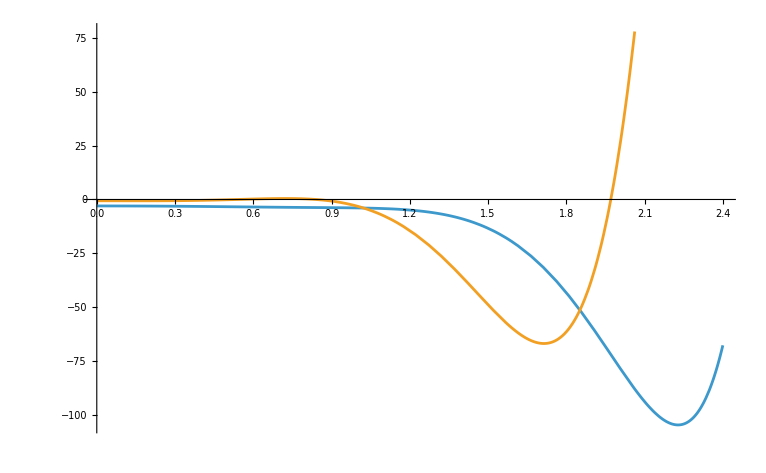

```mathematica
Plot[{Vfun[x]/.{phiM->.6}(*,Vfun'[x]/.{phiM->.6}*),1/5 Vfun''[x]/.{phiM->.6}},{x,0,2.4}]
```

```mathematica
Plot[]
```

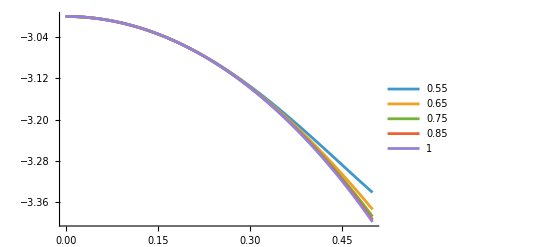

```mathematica
listM={.55,.65,.75, .85,1};
Plot[Evaluate[Vfun[x]/.{phiM->listM}],{x,0,.5},PlotLegends->listM]
```

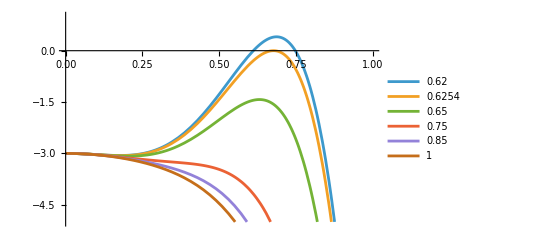

```mathematica
listM={.62,.6254,.65,.75, .85,1};
Plot[Evaluate[Vfun''[x]/.{phiM->listM}],{x,0,1},PlotLegends->listM,PlotRange->{-5,1}]
```

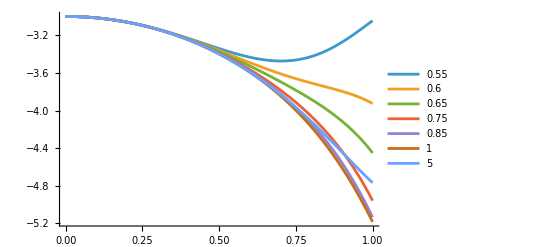

```mathematica
listM={.55,.6,.65,.75, .85,1,5};
Plot[Evaluate[Vfun[x]/.{phiM->listM}],{x,0,1},PlotLegends->listM]
```

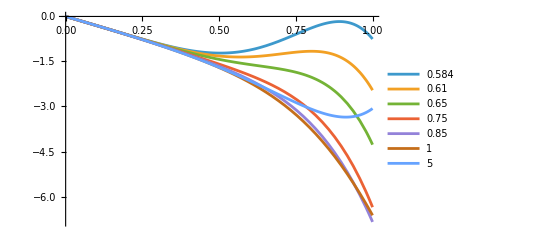

```mathematica
listM={.584,.61,.65,.75, .85,1,5};
Plot[Evaluate[Vfun'[x]/.{phiM->listM}],{x,0,1},PlotLegends->listM]
```

```mathematica
NMaximize[Evaluate[Vfun''[x]//.{phiM->.6254016}],x∈Interval[{0,.8}]]
```

NMaximize::objfs: The objective function {(-1-7.67014 x^2+3 x^4)^2+(-15.3403 x+12 x^3) (-x-2.55671 x^3+(3 x^5)/5)-8/3 (-x-2.55671 Indexed[«2»]^3+3/5 Indexed[«2»]^5)^2-8/3 (-1-7.67014 x^2+3 x^4) (-3/2-x^2/2-0.639178 x^4+x^6/10)} should be scalar-valued.

{-4.81308×10^-6,{x→0.677375}}

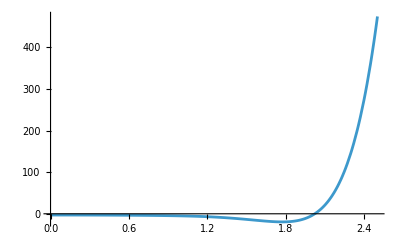

```mathematica
Plot[Evaluate[Vfun[x]/.{phiM->.8}],{x,0,2.5},PlotRange->All]
```

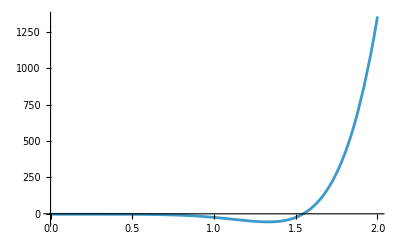

```mathematica
Plot[Evaluate[Vfun''[x]/.{phiM->.8}],{x,0,2},PlotRange->All]
```

```mathematica
Interval[{0,.8}]
```

Interval[{0,0.8}]

```mathematica
Vfun''[x]//.{phiM->hM,x->h}//Simplify//FortranForm
```

-3 - 4*h**2 - (44*h**10)/25. + h**4*(-6 + 15/hM**4 - 10/hM**2) + h**8*(16.2 + 6/hM**2) + (14*h**6*(-5 - 36*hM**2 + 8*hM**4))/(15.*hM**4)

```mathematica
DSolve[f'[x]/f[x]==§/(2h[x]),f[x],x,Assumptions->h[x]<0]
```

{{f[x]→ⅈ C[1] √(-h[x])}}

```mathematica
DSolve[f'[x]/f[x]==h'[x]/h[x],f[x],f[x]]
```